```mathematica
Quit[];
```

```mathematica
ClearAll[dir];
dir=If[DirectoryQ[#],#,CreateDirectory[#]]&@FileNameJoin[{NotebookDirectory[],"Int"}]
```

/home/bwu/Documents/pp/v2/ppv2/Int

## J2

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM"
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

## Analytic J2 (from oneGluon_dipole.nb)

```mathematica
F1s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=1/(4 π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-Log[(bx+x1-x3)^2+(by+y1-y3)^2]+Log[(bx+x1-x4)^2+(by+y1-y4)^2])+ⅇ^(-ⅈ (kx x2+ky y2)) (Log[(bx+x2-x3)^2+(by+y2-y3)^2]-Log[(bx+x2-x4)^2+(by+y2-y4)^2]))
F2s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=(1/(4 (kx^2+ky^2) π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-(1+ⅇ^(ⅈ (kx (bx+x1-x3)+ky (by+y1-y3)))) (EulerGamma+Log[π]+Log[(bx+x1-x3)^2+(by+y1-y3)^2]+2 Log[μ])+(1+ⅇ^(ⅈ (kx (bx+x1-x4)+ky (by+y1-y4)))) (EulerGamma+Log[π]+Log[(bx+x1-x4)^2+(by+y1-y4)^2]+2 Log[μ])+ⅇ^(1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])) (CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅇ^Abs[ky (bx+x1-x3)-kx (by+y1-y3)] (CosIntegral[1/2 (-kx (bx+x1-x3)-ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]))-ⅇ^(1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])) (CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅇ^Abs[ky (bx+x1-x4)-kx (by+y1-y4)] (CosIntegral[1/2 (-kx (bx+x1-x4)-ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])])))+ⅇ^(-ⅈ (kx x2+ky y2)) ((1+ⅇ^(ⅈ (kx (bx+x2-x3)+ky (by+y2-y3)))) (EulerGamma+Log[π]+Log[(bx+x2-x3)^2+(by+y2-y3)^2]+2 Log[μ])-(1+ⅇ^(ⅈ (kx (bx+x2-x4)+ky (by+y2-y4)))) (EulerGamma+Log[π]+Log[(bx+x2-x4)^2+(by+y2-y4)^2]+2 Log[μ])-ⅇ^(1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])) (CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅇ^Abs[ky (bx+x2-x3)-kx (by+y2-y3)] (CosIntegral[1/2 (-kx (bx+x2-x3)-ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]))+ⅇ^(1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])) (CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅇ^Abs[ky (bx+x2-x4)-kx (by+y2-y4)] (CosIntegral[1/2 (-kx (bx+x2-x4)-ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])])))))/.{μ->1}
F2u[{x_,y_},{kx_,ky_}]:=
{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))};
F2us[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]=((F2u[{bx+x1-x3,by+y1-y3},{kx,ky}]-F2u[{bx-x4+x1,by-y4+y1},{kx,ky}]) Exp[-I (kx x1+ky y1)]-(F2u[{bx-x3+x2,by-y3+y2},{kx,ky}]-F2u[{bx-x4+x2,by-y4+y2},{kx,ky}]) Exp[-I (kx x2+ky y2)]
)/.{μ->1};
```

```mathematica
J[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]={kx,ky}/(kx^2+ky^2)F1s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]-
({kx,ky}F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]+I F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]);
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
J2[{kx_,ky_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}];
amp.Conjugate[amp]
]
```

## Comparison

```mathematica
J2HZ[{kx_,ky_},{bx_,by_},{x1x_,x1y_},{x2x_,x2y_},{x3x_,x3y_},{x4x_,x4y_}]:=1/(kx^2+ky^2)J2CompileN[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
```

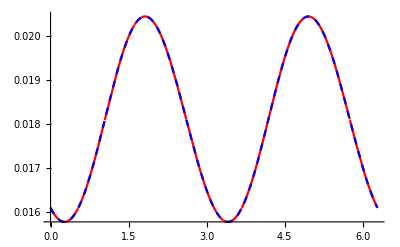

```mathematica
Plot[{J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}],J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]},{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

```mathematica
0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-Graphics-
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression -(ⅈ (0.+0. ⅈ) ComplexInfinity)/(4 π) encountered.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

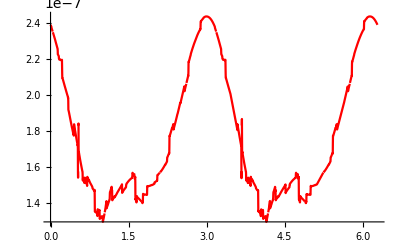

```mathematica
Plot[J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1,{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

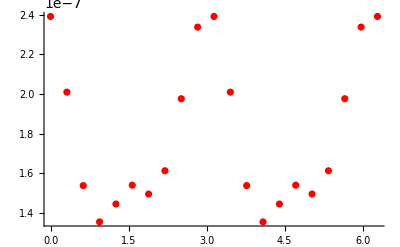

```mathematica
ListPlot[Table[{ϕ,J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1},{ϕ,0,2π,0.1π}],PlotStyle->{{Red},{Blue,Dashed}}]
```

## Dipole Cross Section

```mathematica
dσ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
dσHZ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
J2HZ[{kT Cos[ϕ],kT Sin[ϕ]},{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]
]
```

```mathematica
showdσ[bu_,x1u_,x3u_,kT_]:=Module[{ϕ,x2u,x4u,v2},
x2u=-x1u;x4u=-x3u;
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[Plot[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]];
Print[ParametricPlot[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
v2=NIntegrate[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
Print["v_2=",v2];
v2
]
```

```mathematica
showdσHZ[bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]
]
```

```mathematica
showdσHZ[n_,bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[n(ϕ)],Sin[n(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]
]
```

## b=2 r_dp

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,i,kT,x1u,x3u,bu},
v2kTb05={{0.0,{0.0,0.0}}};
For[i=1,i≤120,i++,
x1u=(1/2){Cos[θA],Sin[θA]};
x3u=(1/2){Cos[θB],Sin[θB]};
bu={b,0};
kT=0.25*i;
AppendTo[v2kTb05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
Print["b=",b, ", θA=",θA,", θB=",θB];
v2kTb05
]
```

```mathematica
showdσHZ[{1.0,0},{0.5,0.5},{1.0,0},1.0,False]
```

{-0.0908371,-0.224816}

```mathematica
Sort[{-0.09083710410936864,-0.22481587914220424}]
```

{-0.224816,-0.0908371}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$4732970 near {ϕ$4732970} = {1.10437}. NIntegrate obtained -9.43256×10^-18 and 2.43631×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$4802107 near {ϕ$4802107} = {1.11664}. NIntegrate obtained 7.96838×10^-14 and 1.31915×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$4853737 near {ϕ$4853737} = {2.19656}. NIntegrate obtained 1.37482×10^-14 and 2.20778×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

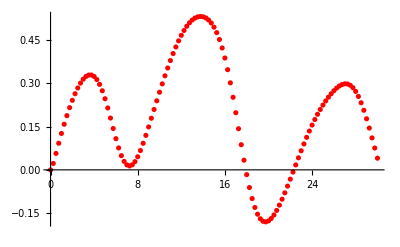

b=0.5, θA=0, θB=π/2

{{0.,{0.,0.}},{0.25,{0.0221996,-3.23371×10^-16}},{0.5,{0.0570201,2.45458×10^-12}},{0.75,{0.0924455,4.00548×10^-13}},{1.,{0.126369,-6.22923×10^-18}},{1.25,{0.158359,-8.20582×10^-17}},{1.5,{0.188286,-2.95008×10^-12}},{1.75,{0.216041,-5.84337×10^-10}},{2.,{0.241466,-4.17965×10^-12}},{2.25,{0.264347,-1.7678×10^-14}},{2.5,{0.284411,-7.59937×10^-18}},{2.75,{0.30133,4.54418×10^-12}},{3.,{0.314724,4.55711×10^-12}},{3.25,{0.324169,1.43257×10^-9}},{3.5,{0.32921,1.30203×10^-17}},{3.75,{0.329386,6.39768×10^-9}},{4.,{0.324269,4.10414×10^-12}},{4.25,{0.313515,-6.18532×10^-17}},{4.5,{0.296944,-1.82982×10^-9}},{4.75,{0.274634,1.20098×10^-12}},{5.,{0.247021,3.59797×10^-11}},{5.25,{0.214987,1.42508×10^-9}},{5.5,{0.179908,2.88088×10^-12}},{5.75,{0.143619,-1.64378×10^-9}},{6.,{0.108286,2.00813×10^-11}},{6.25,{0.0761718,1.36664×10^-8}},{6.5,{0.0493521,-2.77871×10^-10}},{6.75,{0.0294468,5.09257×10^-11}},{7.,{0.017435,5.834×10^-12}},{7.25,{0.0135951,1.81532×10^-8}},{7.5,{0.0175805,-4.21426×10^-8}},{7.75,{0.0285727,5.27911×10^-11}},{8.,{0.0454757,2.86761×10^-8}},{8.25,{0.0670884,3.77256×10^-11}},{8.5,{0.0922415,-1.24882×10^-10}},{8.75,{0.119882,-1.0731×10^-10}},{9.,{0.149113,2.15116×10^-10}},{9.25,{0.179206,2.30835×10^-10}},{9.5,{0.209589,-2.16329×10^-9}},{9.75,{0.239822,6.95511×10^-9}},{10.,{0.269576,2.40401×10^-8}},{10.25,{0.298601,2.67795×10^-10}},{10.5,{0.326704,2.27408×10^-10}},{10.75,{0.353727,-1.14827×10^-8}},{11.,{0.379522,-3.93818×10^-11}},{11.25,{0.403939,-5.71563×10^-10}},{11.5,{0.42681,6.79603×10^-9}},{11.75,{0.447942,9.37176×10^-9}},{12.,{0.467118,-2.70399×10^-10}},{12.25,{0.484117,1.84624×10^-9}},{12.5,{0.498729,6.41399×10^-11}},{12.75,{0.510797,-2.6307×10^-10}},{13.,{0.52023,1.94169×10^-10}},{13.25,{0.527012,2.48967×10^-9}},{13.5,{0.531166,-6.55033×10^-10}},{13.75,{0.532708,7.70974×10^-8}},{14.,{0.531583,7.16468×10^-10}},{14.25,{0.527632,4.16582×10^-8}},{14.5,{0.520575,4.84173×10^-10}},{14.75,{0.510019,6.18242×10^-8}},{15.,{0.495495,-2.55434×10^-10}},{15.25,{0.476498,1.22061×10^-9}},{15.5,{0.452544,-4.44731×10^-10}},{15.75,{0.423239,7.1037×10^-10}},{16.,{0.38835,3.07023×10^-7}},{16.25,{0.347891,6.19011×10^-10}},{16.5,{0.302197,7.10515×10^-9}},{16.75,{0.251988,1.20482×10^-8}},{17.,{0.198389,-9.82006×10^-10}},{17.25,{0.1429,-2.89299×10^-9}},{17.5,{0.0873091,-8.32899×10^-10}},{17.75,{0.0335223,-8.56629×10^-10}},{18.,{-0.0165947,4.04049×10^-8}},{18.25,{-0.0614151,3.80142×10^-8}},{18.5,{-0.0996968,-1.96062×10^-9}},{18.75,{-0.130642,-2.08509×10^-9}},{19.,{-0.153978,5.29826×10^-10}},{19.25,{-0.169779,-3.04424×10^-9}},{19.5,{-0.178478,5.3309×10^-10}},{19.75,{-0.18073,-3.82875×10^-8}},{20.,{-0.177303,-1.82994×10^-9}},{20.25,{-0.169014,-4.73431×10^-9}},{20.5,{-0.156644,-8.31918×10^-9}},{20.75,{-0.140932,-6.51649×10^-9}},{21.,{-0.122525,-1.97073×10^-9}},{21.25,{-0.102002,-5.87279×10^-9}},{21.5,{-0.079854,2.15905×10^-9}},{21.75,{-0.0565126,-2.7443×10^-9}},{22.,{-0.0323491,-1.28922×10^-8}},{22.25,{-0.00769936,1.02072×10^-8}},{22.5,{0.017134,-8.94704×10^-9}},{22.75,{0.0418644,-1.19515×10^-8}},{23.,{0.0662379,-3.67112×10^-9}},{23.25,{0.0899928,1.82462×10^-8}},{23.5,{0.112905,-5.28397×10^-9}},{23.75,{0.134781,-2.38656×10^-8}},{24.,{0.155465,-8.15137×10^-9}},{24.25,{0.174857,3.49973×10^-8}},{24.5,{0.192907,-1.42864×10^-8}},{24.75,{0.209629,-9.98399×10^-9}},{25.,{0.225061,-4.47209×10^-10}},{25.25,{0.239268,-7.57695×10^-10}},{25.5,{0.252289,-2.00509×10^-8}},{25.75,{0.264121,-1.768×10^-8}},{26.,{0.27468,-2.09888×10^-8}},{26.25,{0.283777,-1.27144×10^-8}},{26.5,{0.291114,-6.64079×10^-9}},{26.75,{0.296292,-1.30231×10^-8}},{27.,{0.298821,1.81283×10^-7}},{27.25,{0.29817,-4.55412×10^-9}},{27.5,{0.293819,-1.13286×10^-8}},{27.75,{0.28533,-6.31555×10^-8}},{28.,{0.272378,-1.83807×10^-8}},{28.25,{0.254887,1.38391×10^-8}},{28.5,{0.232939,-2.53063×10^-8}},{28.75,{0.206923,-2.12846×10^-8}},{29.,{0.177415,-2.33819×10^-8}},{29.25,{0.145154,-6.32264×10^-8}},{29.5,{0.111,-3.97756×10^-8}},{29.75,{0.0758315,-8.03388×10^-8}},{30.,{0.0405409,-9.46502×10^-8}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$13453024 near {ϕ$13453024} = {2.71198}. NIntegrate obtained -4.77961×10^-6 and 8.22802×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$14326236 near {ϕ$14326236} = {1.28845}. NIntegrate obtained 3.50731×10^-6 and 5.85175×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$14401908 near {ϕ$14401908} = {1.25163}. NIntegrate obtained -3.54072×10^-6 and 5.48343×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

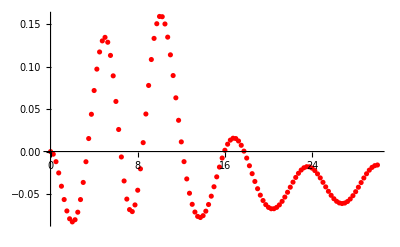

b=0.5, θA=π/4, θB=π/2

{{0.,{0.,0.}},{0.25,{-0.00309306,0.000750954}},{0.5,{-0.0119145,0.00323082}},{0.75,{-0.0251503,0.00778633}},{1.,{-0.0407959,0.0146037}},{1.25,{-0.0564838,0.0236247}},{1.5,{-0.0698936,0.0345614}},{1.75,{-0.0791022,0.0469708}},{2.,{-0.0827828,0.0603467}},{2.25,{-0.0802443,0.0741943}},{2.5,{-0.0713666,0.0880696}},{2.75,{-0.0564958,0.101583}},{3.,{-0.0363525,0.114382}},{3.25,{-0.0119737,0.126112}},{3.5,{0.0153099,0.136383}},{3.75,{0.0438767,0.14473}},{4.,{0.0718237,0.150591}},{4.25,{0.0970151,0.153302}},{4.5,{0.117202,0.152123}},{4.75,{0.130237,0.1463}},{5.,{0.134382,0.135169}},{5.25,{0.128653,0.118278}},{5.5,{0.113128,0.0955099}},{5.75,{0.0890952,0.0671641}},{6.,{0.0589675,0.0339598}},{6.25,{0.0259637,-0.00303082}},{6.5,{-0.00636037,-0.0425091}},{6.75,{-0.0346051,-0.0830886}},{7.,{-0.0559293,-0.123408}},{7.25,{-0.0683078,-0.1622}},{7.5,{-0.0706468,-0.198316}},{7.75,{-0.0627976,-0.230726}},{8.,{-0.0455087,-0.25852}},{8.25,{-0.0203369,-0.28091}},{8.5,{0.0104769,-0.297281}},{8.75,{0.0441866,-0.30725}},{9.,{0.0777857,-0.31074}},{9.25,{0.10831,-0.308032}},{9.5,{0.133165,-0.299786}},{9.75,{0.150415,-0.286994}},{10.,{0.158979,-0.270878}},{10.25,{0.158677,-0.252744}},{10.5,{0.150148,-0.233893}},{10.75,{0.13465,-0.215388}},{11.,{0.113818,-0.198094}},{11.25,{0.0894324,-0.182594}},{11.5,{0.0632309,-0.16921}},{11.75,{0.0367771,-0.15804}},{12.,{0.0113944,-0.149014}},{12.25,{-0.0118613,-0.141937}},{12.5,{-0.0321957,-0.136534}},{12.75,{-0.0490539,-0.132495}},{13.,{-0.0620966,-0.129492}},{13.25,{-0.0711709,-0.127212}},{13.5,{-0.0762895,-0.125364}},{13.75,{-0.0776124,-0.123699}},{14.,{-0.075432,-0.122011}},{14.25,{-0.0701604,-0.120151}},{14.5,{-0.0623166,-0.118024}},{14.75,{-0.0525101,-0.115599}},{15.,{-0.0414185,-0.112896}},{15.25,{-0.0297618,-0.109991}},{15.5,{-0.0182676,-0.106998}},{15.75,{-0.00763233,-0.104064}},{16.,{0.00151965,-0.101345}},{16.25,{0.0086746,-0.0989941}},{16.5,{0.0134627,-0.0971431}},{16.75,{0.0156781,-0.0958875}},{17.,{0.0152884,-0.0952776}},{17.25,{0.012426,-0.0953131}},{17.5,{0.00736878,-0.0959473}},{17.75,{0.000509203,-0.0970909}},{18.,{-0.0076832,-0.098627}},{18.25,{-0.0166995,-0.100421}},{18.5,{-0.0260281,-0.102337}},{18.75,{-0.0351842,-0.104249}},{19.,{-0.0437339,-0.106058}},{19.25,{-0.0513106,-0.107693}},{19.5,{-0.0576251,-0.109106}},{19.75,{-0.0624678,-0.110311}},{20.,{-0.0657108,-0.111344}},{20.25,{-0.0673041,-0.112277}},{20.5,{-0.0672705,-0.113215}},{20.75,{-0.0657009,-0.114287}},{21.,{-0.0627481,-0.115641}},{21.25,{-0.05862,-0.11743}},{21.5,{-0.0535727,-0.119807}},{21.75,{-0.047901,-0.122914}},{22.,{-0.0419298,-0.126866}},{22.25,{-0.0359991,-0.131747}},{22.5,{-0.0304494,-0.137595}},{22.75,{-0.0256031,-0.144399}},{23.,{-0.0217446,-0.152091}},{23.25,{-0.0191014,-0.160555}},{23.5,{-0.0178255,-0.169624}},{23.75,{-0.0179808,-0.179103}},{24.,{-0.0195371,-0.188777}},{24.25,{-0.0223728,-0.198435}},{24.5,{-0.0262829,-0.207887}},{24.75,{-0.0309998,-0.216986}},{25.,{-0.0362106,-0.225626}},{25.25,{-0.0415831,-0.233769}},{25.5,{-0.0467888,-0.241428}},{25.75,{-0.0515212,-0.248673}},{26.,{-0.0555133,-0.255622}},{26.25,{-0.0585455,-0.262423}},{26.5,{-0.0604585,-0.269252}},{26.75,{-0.0611517,-0.276295}},{27.,{-0.0605893,-0.283741}},{27.25,{-0.0587953,-0.291756}},{27.5,{-0.0558612,-0.300489}},{27.75,{-0.0519352,-0.310052}},{28.,{-0.0472221,-0.320516}},{28.25,{-0.0419795,-0.331882}},{28.5,{-0.0365029,-0.344105}},{28.75,{-0.0311151,-0.357068}},{29.,{-0.0261444,-0.370597}},{29.25,{-0.0219013,-0.384455}},{29.5,{-0.0186537,-0.398367}},{29.75,{-0.0165963,-0.412035}},{30.,{-0.0158339,-0.425163}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$23287869 near {ϕ$23287869} = {2.57699}. NIntegrate obtained -2.01977×10^-13 and 2.53476×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$23363984 near {ϕ$23363984} = {0.638038}. NIntegrate obtained 5.67255×10^-15 and 1.25353×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$23444609 near {ϕ$23444609} = {4.23369}. NIntegrate obtained 4.41921×10^-15 and 5.51898×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

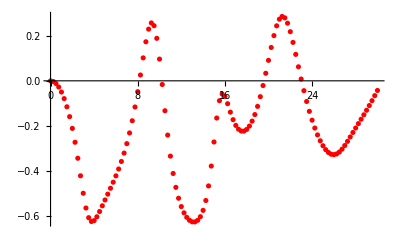

b=0.5, θA=π/2, θB=π/2

{{0.,{0.,0.}},{0.25,{-0.00293846,-3.22266×10^-14}},{0.5,{-0.0119878,4.01797×10^-15}},{0.75,{-0.0274896,8.05572×10^-15}},{1.,{-0.0496732,3.74359×10^-14}},{1.25,{-0.0786963,4.28793×10^-14}},{1.5,{-0.114789,-6.03624×10^-13}},{1.75,{-0.158429,-3.55129×10^-17}},{2.,{-0.210431,2.61653×10^-12}},{2.25,{-0.271718,-1.06398×10^-12}},{2.5,{-0.342421,-5.93236×10^-11}},{2.75,{-0.420021,3.5364×10^-11}},{3.,{-0.497264,7.23561×10^-12}},{3.25,{-0.562566,-7.13039×10^-9}},{3.5,{-0.605292,1.42908×10^-9}},{3.75,{-0.62223,-4.08025×10^-9}},{4.,{-0.618239,-5.81003×10^-10}},{4.25,{-0.601331,1.24109×10^-9}},{4.5,{-0.578195,4.04457×10^-9}},{4.75,{-0.552817,-3.57247×10^-11}},{5.,{-0.526988,1.47112×10^-9}},{5.25,{-0.501173,3.04482×10^-9}},{5.5,{-0.47516,1.02292×10^-10}},{5.75,{-0.448418,-7.07705×10^-11}},{6.,{-0.420273,1.03417×10^-8}},{6.25,{-0.389976,1.79615×10^-8}},{6.5,{-0.356724,-3.05977×10^-9}},{6.75,{-0.319663,-4.44271×10^-11}},{7.,{-0.277894,-2.47251×10^-11}},{7.25,{-0.230502,2.16695×10^-10}},{7.5,{-0.176646,-2.85718×10^-10}},{7.75,{-0.115746,2.7498×10^-12}},{8.,{-0.0478498,-1.51385×10^-10}},{8.25,{0.0257362,5.98577×10^-10}},{8.5,{0.101504,-3.03453×10^-10}},{8.75,{0.172664,1.71001×10^-10}},{9.,{0.228584,-4.39478×10^-8}},{9.25,{0.256093,-1.35779×10^-10}},{9.5,{0.243768,1.80117×10^-10}},{9.75,{0.187961,2.44382×10^-10}},{10.,{0.0961155,-3.32592×10^-9}},{10.25,{-0.0161986,9.39926×10^-10}},{10.5,{-0.132316,-8.89064×10^-10}},{10.75,{-0.240029,1.53059×10^-9}},{11.,{-0.333077,-8.73849×10^-11}},{11.25,{-0.409818,2.59413×10^-8}},{11.5,{-0.471218,-5.93729×10^-11}},{11.75,{-0.519297,-1.65977×10^-7}},{12.,{-0.55623,3.20114×10^-14}},{12.25,{-0.58392,-9.15752×10^-10}},{12.5,{-0.603832,-1.34332×10^-10}},{12.75,{-0.616939,-5.77897×10^-9}},{13.,{-0.623691,8.20746×10^-9}},{13.25,{-0.623961,-9.89742×10^-9}},{13.5,{-0.616931,-9.21197×10^-9}},{13.75,{-0.600898,-5.27947×10^-10}},{14.,{-0.57304,-8.64402×10^-9}},{14.25,{-0.529286,-1.75417×10^-9}},{14.5,{-0.464894,1.09976×10^-9}},{14.75,{-0.376998,-3.81623×10^-9}},{15.,{-0.270524,5.50331×10^-9}},{15.25,{-0.164605,-3.38064×10^-9}},{15.5,{-0.087889,-3.76231×10^-9}},{15.75,{-0.058007,-3.55694×10^-9}},{16.,{-0.068785,2.06293×10^-9}},{16.25,{-0.101157,-1.31209×10^-9}},{16.5,{-0.13856,2.46724×10^-8}},{16.75,{-0.171809,-1.55624×10^-7}},{17.,{-0.197223,1.84117×10^-8}},{17.25,{-0.213924,-1.32234×10^-8}},{17.5,{-0.222123,-6.69793×10^-9}},{17.75,{-0.2223,9.57063×10^-9}},{18.,{-0.21489,-6.14174×10^-8}},{18.25,{-0.200167,7.39934×10^-9}},{18.5,{-0.178263,-2.05153×10^-9}},{18.75,{-0.149237,4.9509×10^-9}},{19.,{-0.113092,-1.16386×10^-8}},{19.25,{-0.070118,-3.76135×10^-9}},{19.5,{-0.0208926,-9.86587×10^-9}},{19.75,{0.0333654,-2.04069×10^-9}},{20.,{0.0905492,-4.21111×10^-9}},{20.25,{0.147491,-1.285×10^-8}},{20.5,{0.199981,-2.5641×10^-8}},{20.75,{0.243209,-8.28052×10^-9}},{21.,{0.272559,-2.52265×10^-8}},{21.25,{0.284694,-2.42728×10^-8}},{21.5,{0.278405,1.94579×10^-8}},{21.75,{0.254908,-4.16011×10^-8}},{22.,{0.217366,-1.3882×10^-8}},{22.25,{0.169974,-9.59871×10^-9}},{22.5,{0.116993,-3.66937×10^-8}},{22.75,{0.062076,2.75005×10^-8}},{23.,{0.00794649,-3.01615×10^-8}},{23.25,{-0.0435514,1.25449×10^-8}},{23.5,{-0.0913512,-1.59653×10^-8}},{23.75,{-0.134919,4.47874×10^-9}},{24.,{-0.174075,-2.16859×10^-8}},{24.25,{-0.208816,5.94535×10^-8}},{24.5,{-0.239213,-8.45132×10^-8}},{24.75,{-0.26531,3.69644×10^-8}},{25.,{-0.287072,-1.98294×10^-8}},{25.25,{-0.304354,-8.21445×10^-7}},{25.5,{-0.316903,3.54906×10^-9}},{25.75,{-0.324407,-4.23101×10^-9}},{26.,{-0.326601,-2.85156×10^-8}},{26.25,{-0.323405,6.47479×10^-9}},{26.5,{-0.315083,-3.31133×10^-7}},{26.75,{-0.302306,-1.48647×10^-8}},{27.,{-0.286127,-1.17954×10^-8}},{27.25,{-0.267735,3.28228×10^-8}},{27.5,{-0.248234,2.31983×10^-8}},{27.75,{-0.228432,-6.87637×10^-7}},{28.,{-0.208734,-4.3891×10^-8}},{28.25,{-0.189261,-4.57546×10^-8}},{28.5,{-0.169846,-4.8988×10^-7}},{28.75,{-0.150243,1.1607×10^-7}},{29.,{-0.130176,6.18468×10^-8}},{29.25,{-0.109409,-1.70999×10^-8}},{29.5,{-0.0878411,1.65943×10^-8}},{29.75,{-0.0654788,-2.8936×10^-7}},{30.,{-0.04255,3.99352×10^-8}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$31479011 near {ϕ$31479011} = {3.58328}. NIntegrate obtained 4.77961×10^-6 and 8.22802×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32352373 near {ϕ$32352373} = {1.86522}. NIntegrate obtained 3.50731×10^-6 and 5.85175×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32428045 near {ϕ$32428045} = {1.90204}. NIntegrate obtained -3.54072×10^-6 and 5.48343×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-Graphics-

b=0.5, θA=(3 π)/4, θB=π/2

{{0.,{0.,0.}},{0.25,{-0.00309306,-0.000750954}},{0.5,{-0.0119145,-0.00323082}},{0.75,{-0.0251503,-0.00778633}},{1.,{-0.0407959,-0.0146037}},{1.25,{-0.0564838,-0.0236247}},{1.5,{-0.0698936,-0.0345614}},{1.75,{-0.0791022,-0.0469708}},{2.,{-0.0827828,-0.0603467}},{2.25,{-0.0802443,-0.0741943}},{2.5,{-0.0713666,-0.0880696}},{2.75,{-0.0564958,-0.101583}},{3.,{-0.0363525,-0.114382}},{3.25,{-0.0119737,-0.126112}},{3.5,{0.0153099,-0.136383}},{3.75,{0.0438767,-0.14473}},{4.,{0.0718237,-0.150591}},{4.25,{0.0970151,-0.153302}},{4.5,{0.117202,-0.152123}},{4.75,{0.130237,-0.1463}},{5.,{0.134382,-0.135169}},{5.25,{0.128653,-0.118278}},{5.5,{0.113128,-0.0955099}},{5.75,{0.0890952,-0.0671641}},{6.,{0.0589675,-0.0339598}},{6.25,{0.0259637,0.00303082}},{6.5,{-0.00636037,0.0425091}},{6.75,{-0.0346051,0.0830886}},{7.,{-0.0559293,0.123408}},{7.25,{-0.0683078,0.1622}},{7.5,{-0.0706468,0.198316}},{7.75,{-0.0627976,0.230726}},{8.,{-0.0455087,0.25852}},{8.25,{-0.0203369,0.28091}},{8.5,{0.0104769,0.297281}},{8.75,{0.0441866,0.30725}},{9.,{0.0777857,0.31074}},{9.25,{0.10831,0.308032}},{9.5,{0.133165,0.299786}},{9.75,{0.150415,0.286994}},{10.,{0.158979,0.270878}},{10.25,{0.158677,0.252744}},{10.5,{0.150148,0.233893}},{10.75,{0.13465,0.215388}},{11.,{0.113818,0.198094}},{11.25,{0.0894324,0.182594}},{11.5,{0.0632309,0.16921}},{11.75,{0.0367771,0.15804}},{12.,{0.0113944,0.149014}},{12.25,{-0.0118613,0.141937}},{12.5,{-0.0321957,0.136534}},{12.75,{-0.0490539,0.132495}},{13.,{-0.0620966,0.129492}},{13.25,{-0.0711709,0.127212}},{13.5,{-0.0762895,0.125364}},{13.75,{-0.0776124,0.123699}},{14.,{-0.075432,0.122011}},{14.25,{-0.0701604,0.120151}},{14.5,{-0.0623166,0.118024}},{14.75,{-0.0525101,0.115599}},{15.,{-0.0414185,0.112896}},{15.25,{-0.0297618,0.109991}},{15.5,{-0.0182676,0.106998}},{15.75,{-0.00763233,0.104064}},{16.,{0.00151965,0.101345}},{16.25,{0.0086746,0.0989941}},{16.5,{0.0134627,0.0971431}},{16.75,{0.0156781,0.0958875}},{17.,{0.0152884,0.0952776}},{17.25,{0.012426,0.0953131}},{17.5,{0.00736878,0.0959473}},{17.75,{0.000509203,0.0970909}},{18.,{-0.0076832,0.098627}},{18.25,{-0.0166995,0.100421}},{18.5,{-0.0260281,0.102337}},{18.75,{-0.0351842,0.104249}},{19.,{-0.0437339,0.106058}},{19.25,{-0.0513106,0.107693}},{19.5,{-0.0576251,0.109106}},{19.75,{-0.0624678,0.110311}},{20.,{-0.0657108,0.111344}},{20.25,{-0.0673041,0.112277}},{20.5,{-0.0672705,0.113215}},{20.75,{-0.0657009,0.114287}},{21.,{-0.0627481,0.115641}},{21.25,{-0.05862,0.11743}},{21.5,{-0.0535727,0.119807}},{21.75,{-0.047901,0.122914}},{22.,{-0.0419298,0.126866}},{22.25,{-0.0359991,0.131747}},{22.5,{-0.0304494,0.137595}},{22.75,{-0.0256031,0.144399}},{23.,{-0.0217446,0.152091}},{23.25,{-0.0191014,0.160555}},{23.5,{-0.0178255,0.169624}},{23.75,{-0.0179808,0.179103}},{24.,{-0.0195371,0.188777}},{24.25,{-0.0223728,0.198435}},{24.5,{-0.0262829,0.207887}},{24.75,{-0.0309998,0.216986}},{25.,{-0.0362106,0.225626}},{25.25,{-0.0415831,0.233769}},{25.5,{-0.0467888,0.241428}},{25.75,{-0.0515212,0.248673}},{26.,{-0.0555133,0.255622}},{26.25,{-0.0585455,0.262423}},{26.5,{-0.0604585,0.269252}},{26.75,{-0.0611517,0.276295}},{27.,{-0.0605893,0.283741}},{27.25,{-0.0587953,0.291756}},{27.5,{-0.0558612,0.300489}},{27.75,{-0.0519352,0.310052}},{28.,{-0.0472221,0.320516}},{28.25,{-0.0419795,0.331882}},{28.5,{-0.0365029,0.344105}},{28.75,{-0.0311151,0.357068}},{29.,{-0.0261444,0.370597}},{29.25,{-0.0219013,0.384455}},{29.5,{-0.0186537,0.398367}},{29.75,{-0.0165963,0.412035}},{30.,{-0.0158339,0.425163}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$41855730 near {ϕ$41855730} = {3.706}. NIntegrate obtained 0.0000174075 and 2.79255×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$42202313 near {ϕ$42202313} = {4.02507}. NIntegrate obtained 6.7048×10^-7 and 1.24737×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$42374351 near {ϕ$42374351} = {0.588951}. NIntegrate obtained 0.0000128466 and 1.63382×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

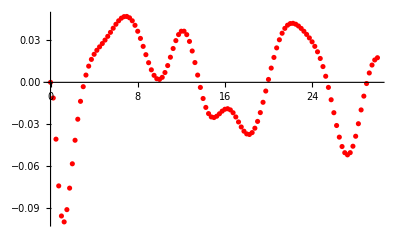

b=0.5, θA=0, θB=π/4

{{0.,{0.,0.}},{0.25,{-0.0112139,-0.00584268}},{0.5,{-0.0407056,-0.0245241}},{0.75,{-0.0742113,-0.0542608}},{1.,{-0.09576,-0.0882517}},{1.25,{-0.1,-0.120056}},{1.5,{-0.0912173,-0.147254}},{1.75,{-0.0757954,-0.17022}},{2.,{-0.0583624,-0.190019}},{2.25,{-0.0414953,-0.207439}},{2.5,{-0.0264157,-0.222791}},{2.75,{-0.0135933,-0.235985}},{3.,{-0.00309861,-0.246637}},{3.25,{0.00521327,-0.254176}},{3.5,{0.0116126,-0.257949}},{3.75,{0.016446,-0.257324}},{4.,{0.0201021,-0.251803}},{4.25,{0.0229785,-0.241133}},{4.5,{0.0254458,-0.225391}},{4.75,{0.0278109,-0.205032}},{5.,{0.0302855,-0.180878}},{5.25,{0.032968,-0.154042}},{5.5,{0.0358413,-0.12582}},{5.75,{0.0387878,-0.0975503}},{6.,{0.0416173,-0.0704962}},{6.25,{0.0440996,-0.0457561}},{6.5,{0.045998,-0.0242196}},{6.75,{0.0470971,-0.0065574}},{7.,{0.0472189,0.00675182}},{7.25,{0.0462471,0.0153934}},{7.5,{0.0441278,0.0191694}},{7.75,{0.040881,0.0179685}},{8.,{0.0366047,0.0117395}},{8.25,{0.0314803,0.000483823}},{8.5,{0.0257737,-0.0157431}},{8.75,{0.0198334,-0.0368116}},{9.,{0.0140798,-0.0624919}},{9.25,{0.00898108,-0.0924161}},{9.5,{0.00501537,-0.126051}},{9.75,{0.00261489,-0.162674}},{10.,{0.00209823,-0.201387}},{10.25,{0.00360239,-0.241158}},{10.5,{0.00702994,-0.280898}},{10.75,{0.0120283,-0.319567}},{11.,{0.0180148,-0.356279}},{11.25,{0.0242443,-0.390377}},{11.5,{0.0299079,-0.421467}},{11.75,{0.0342423,-0.449396}},{12.,{0.0366277,-0.474179}},{12.25,{0.036659,-0.495903}},{12.5,{0.0341878,-0.514627}},{12.75,{0.0293321,-0.530296}},{13.,{0.0224688,-0.542686}},{13.25,{0.0141811,-0.551384}},{13.5,{0.00520976,-0.555821}},{13.75,{-0.00363469,-0.555337}},{14.,{-0.0115727,-0.549279}},{14.25,{-0.0179624,-0.537128}},{14.5,{-0.0223922,-0.518602}},{14.75,{-0.0247474,-0.493736}},{15.,{-0.0252193,-0.462902}},{15.25,{-0.0242632,-0.426772}},{15.5,{-0.0225081,-0.38624}},{15.75,{-0.0206388,-0.342318}},{16.,{-0.0192792,-0.296037}},{16.25,{-0.0188979,-0.248381}},{16.5,{-0.0197337,-0.200246}},{16.75,{-0.021782,-0.152444}},{17.,{-0.0248079,-0.10571}},{17.25,{-0.0283856,-0.0607265}},{17.5,{-0.0319754,-0.0181448}},{17.75,{-0.0350003,0.0214295}},{18.,{-0.036929,0.0574265}},{18.25,{-0.0373469,0.0893504}},{18.5,{-0.0360087,0.1168}},{18.75,{-0.0328512,0.139475}},{19.,{-0.0279891,0.157257}},{19.25,{-0.0216813,0.170073}},{19.5,{-0.0142895,0.177996}},{19.75,{-0.00622847,0.181178}},{20.,{0.00207565,0.179826}},{20.25,{0.0102216,0.174191}},{20.5,{0.0178561,0.164534}},{20.75,{0.024694,0.151144}},{21.,{0.0305214,0.13431}},{21.25,{0.0352031,0.114352}},{21.5,{0.0386785,0.0916179}},{21.75,{0.040961,0.0665119}},{22.,{0.0421237,0.0394972}},{22.25,{0.0423013,0.0111206}},{22.5,{0.041659,-0.0179988}},{22.75,{0.0403847,-0.0471733}},{23.,{0.038653,-0.075708}},{23.25,{0.0366112,-0.102901}},{23.5,{0.0343396,-0.128156}},{23.75,{0.0318477,-0.151032}},{24.,{0.0290547,-0.171281}},{24.25,{0.0257997,-0.188893}},{24.5,{0.0218884,-0.204074}},{24.75,{0.0171128,-0.217211}},{25.,{0.0113013,-0.228786}},{25.25,{0.00436995,-0.239297}},{25.5,{-0.00362143,-0.249153}},{25.75,{-0.0124663,-0.2586}},{26.,{-0.021756,-0.267639}},{26.25,{-0.0309263,-0.276}},{26.5,{-0.0392622,-0.283126}},{26.75,{-0.0459923,-0.288234}},{27.,{-0.0504096,-0.290413}},{27.25,{-0.0519592,-0.288762}},{27.5,{-0.0503835,-0.282555}},{27.75,{-0.0457838,-0.271389}},{28.,{-0.0386206,-0.255254}},{28.25,{-0.0296431,-0.234554}},{28.5,{-0.0197546,-0.209968}},{28.75,{-0.00988171,-0.182428}},{29.,{-0.000847269,-0.152889}},{29.25,{0.00672039,-0.122264}},{29.5,{0.0124078,-0.0913463}},{29.75,{0.01604,-0.0607773}},{30.,{0.0176456,-0.0310573}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$49221318 near {ϕ$49221318} = {1.53388}. NIntegrate obtained -7.35538×10^-6 and 1.08581×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$49512047 near {ϕ$49512047} = {4.89637}. NIntegrate obtained 0.0000247162 and 3.793×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$49623027 near {ϕ$49623027} = {3.37466}. NIntegrate obtained -5.52538×10^-7 and 2.82468×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

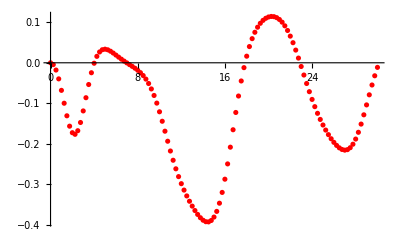

b=0.5, θA=π/4, θB=π/4

{{0.,{0.,0.}},{0.25,{-0.00447884,-0.00171949}},{0.5,{-0.0179197,-0.00708555}},{0.75,{-0.0397211,-0.0164856}},{1.,{-0.0680913,-0.0302315}},{1.25,{-0.099895,-0.0483159}},{1.5,{-0.130918,-0.0701361}},{1.75,{-0.156542,-0.0942516}},{2.,{-0.172676,-0.11828}},{2.25,{-0.176639,-0.139023}},{2.5,{-0.167754,-0.152872}},{2.75,{-0.147453,-0.156453}},{3.,{-0.118905,-0.147393}},{3.25,{-0.0862529,-0.124951}},{3.5,{-0.0536787,-0.0902718}},{3.75,{-0.0245865,-0.0461442}},{4.,{-0.00111986,0.00366089}},{4.25,{0.0158991,0.055189}},{4.5,{0.0267118,0.104955}},{4.75,{0.0322221,0.150306}},{5.,{0.0336128,0.189495}},{5.25,{0.0320703,0.221555}},{5.5,{0.0286269,0.246106}},{5.75,{0.0240974,0.263143}},{6.,{0.0190751,0.272867}},{6.25,{0.013957,0.275569}},{6.5,{0.00897689,0.27155}},{6.75,{0.00424038,0.261079}},{7.,{-0.000253611,0.244383}},{7.25,{-0.00458554,0.221654}},{7.5,{-0.00891146,0.193081}},{7.75,{-0.0134516,0.158896}},{8.,{-0.0184907,0.119452}},{8.25,{-0.0243722,0.0753187}},{8.5,{-0.0314934,0.0274037}},{8.75,{-0.0402861,-0.0229149}},{9.,{-0.0511858,-0.0736715}},{9.25,{-0.0645734,-0.122263}},{9.5,{-0.0807003,-0.165533}},{9.75,{-0.0996002,-0.200052}},{10.,{-0.121022,-0.222622}},{10.25,{-0.144407,-0.230905}},{10.5,{-0.16895,-0.224}},{10.75,{-0.19373,-0.202726}},{11.,{-0.21788,-0.169478}},{11.25,{-0.240721,-0.12771}},{11.5,{-0.261848,-0.0812494}},{11.75,{-0.281112,-0.0336838}},{12.,{-0.298571,0.0120242}},{12.25,{-0.314399,0.0536817}},{12.5,{-0.328805,0.0898243}},{12.75,{-0.341967,0.119576}},{13.,{-0.354001,0.142497}},{13.25,{-0.364899,0.158417}},{13.5,{-0.374536,0.167352}},{13.75,{-0.382649,0.169422}},{14.,{-0.388823,0.164836}},{14.25,{-0.392495,0.153906}},{14.5,{-0.392965,0.13709}},{14.75,{-0.389428,0.115068}},{15.,{-0.381037,0.0888208}},{15.25,{-0.367012,0.0597009}},{15.5,{-0.346783,0.0294521}},{15.75,{-0.320162,0.000144713}},{16.,{-0.287493,-0.0260097}},{16.25,{-0.249735,-0.0469509}},{16.5,{-0.208407,-0.0610967}},{16.75,{-0.165403,-0.0676296}},{17.,{-0.122707,-0.0666488}},{17.25,{-0.0820962,-0.0590808}},{17.5,{-0.044926,-0.0464577}},{17.75,{-0.0120178,-0.0306052}},{18.,{0.016289,-0.0133627}},{18.25,{0.0400529,0.00361791}},{18.5,{0.0595933,0.0189896}},{18.75,{0.0753484,0.0317408}},{19.,{0.087859,0.0411664}},{19.25,{0.0975401,0.046842}},{19.5,{0.104788,0.0485788}},{19.75,{0.109904,0.0463836}},{20.,{0.113081,0.0404471}},{20.25,{0.114416,0.0311371}},{20.5,{0.113907,0.0190035}},{20.75,{0.111483,0.00479611}},{21.,{0.107007,-0.0105347}},{21.25,{0.100323,-0.025842}},{21.5,{0.0912774,-0.0398222}},{21.75,{0.0797814,-0.0510971}},{22.,{0.0658387,-0.0583395}},{22.25,{0.0495994,-0.0604411}},{22.5,{0.031369,-0.0566755}},{22.75,{0.0116055,-0.0468488}},{23.,{-0.00914203,-0.031355}},{23.25,{-0.0302548,-0.0111498}},{23.5,{-0.0511538,0.0123781}},{23.75,{-0.0713547,0.0376014}},{24.,{-0.0904931,0.0628242}},{24.25,{-0.108352,0.0864554}},{24.5,{-0.124825,0.107122}},{24.75,{-0.13991,0.123698}},{25.,{-0.15366,0.135312}},{25.25,{-0.166154,0.141329}},{25.5,{-0.177456,0.141321}},{25.75,{-0.18759,0.135028}},{26.,{-0.196511,0.122368}},{26.25,{-0.204084,0.103444}},{26.5,{-0.210066,0.0786077}},{26.75,{-0.214104,0.0485107}},{27.,{-0.215748,0.014199}},{27.25,{-0.214464,-0.0227864}},{27.5,{-0.20973,-0.0604113}},{27.75,{-0.201111,-0.0961982}},{28.,{-0.188388,-0.127429}},{28.25,{-0.171668,-0.151501}},{28.5,{-0.15142,-0.166332}},{28.75,{-0.128506,-0.170779}},{29.,{-0.104017,-0.164822}},{29.25,{-0.0791118,-0.149541}},{29.5,{-0.0548606,-0.126838}},{29.75,{-0.032092,-0.0990466}},{30.,{-0.011356,-0.0685415}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$57131769 near {ϕ$57131769} = {5.15408}. NIntegrate obtained -4.77966×10^-6 and 7.60031×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$57987759 near {ϕ$57987759} = {1.28845}. NIntegrate obtained 3.50728×10^-6 and 6.20202×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$58062319 near {ϕ$58062319} = {6.17469296672037219753104153596723335795104503631591796875}. NIntegrate obtained -3.54075×10^-6 and 6.35772×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

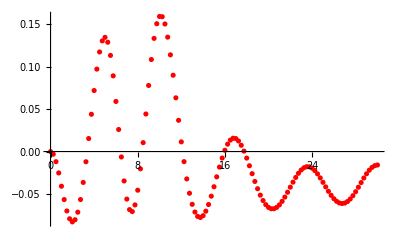

b=0.5, θA=π/2, θB=π/4

{{0.,{0.,0.}},{0.25,{-0.00309306,0.000750924}},{0.5,{-0.0119145,0.00323078}},{0.75,{-0.0251503,0.00778635}},{1.,{-0.0407959,0.0146037}},{1.25,{-0.0564838,0.0236247}},{1.5,{-0.0698936,0.0345615}},{1.75,{-0.0791022,0.0469708}},{2.,{-0.0827828,0.0603467}},{2.25,{-0.0802443,0.0741944}},{2.5,{-0.0713666,0.0880695}},{2.75,{-0.0564957,0.101583}},{3.,{-0.0363526,0.114382}},{3.25,{-0.0119738,0.126112}},{3.5,{0.0153098,0.136383}},{3.75,{0.0438767,0.14473}},{4.,{0.0718236,0.150591}},{4.25,{0.097015,0.153302}},{4.5,{0.117202,0.152123}},{4.75,{0.130237,0.1463}},{5.,{0.134382,0.135169}},{5.25,{0.128652,0.118277}},{5.5,{0.113128,0.09551}},{5.75,{0.0890951,0.067164}},{6.,{0.0589674,0.0339598}},{6.25,{0.0259637,-0.00303085}},{6.5,{-0.00636043,-0.0425092}},{6.75,{-0.0346051,-0.0830886}},{7.,{-0.0559293,-0.123408}},{7.25,{-0.0683078,-0.1622}},{7.5,{-0.0706468,-0.198316}},{7.75,{-0.0627977,-0.230726}},{8.,{-0.0455087,-0.25852}},{8.25,{-0.0203369,-0.28091}},{8.5,{0.0104769,-0.297281}},{8.75,{0.0441865,-0.307251}},{9.,{0.0777857,-0.31074}},{9.25,{0.10831,-0.308032}},{9.5,{0.133165,-0.299786}},{9.75,{0.150415,-0.286994}},{10.,{0.158979,-0.270877}},{10.25,{0.158677,-0.252753}},{10.5,{0.150148,-0.233892}},{10.75,{0.134649,-0.215387}},{11.,{0.113818,-0.198094}},{11.25,{0.0898225,-0.183391}},{11.5,{0.0632308,-0.16921}},{11.75,{0.0367768,-0.158039}},{12.,{0.0113943,-0.149014}},{12.25,{-0.0118614,-0.141936}},{12.5,{-0.0321957,-0.136534}},{12.75,{-0.0490541,-0.132495}},{13.,{-0.0620967,-0.129492}},{13.25,{-0.0711708,-0.127212}},{13.5,{-0.0762895,-0.125364}},{13.75,{-0.0776124,-0.123699}},{14.,{-0.0754321,-0.122011}},{14.25,{-0.0701608,-0.120151}},{14.5,{-0.062317,-0.118024}},{14.75,{-0.0525102,-0.115598}},{15.,{-0.0414184,-0.112896}},{15.25,{-0.0297618,-0.10999}},{15.5,{-0.0182675,-0.106998}},{15.75,{-0.00763215,-0.104063}},{16.,{0.00151987,-0.101344}},{16.25,{0.00867468,-0.0989935}},{16.5,{0.0134628,-0.0971424}},{16.75,{0.0156783,-0.0958867}},{17.,{0.0152882,-0.0952769}},{17.25,{0.0124257,-0.0953124}},{17.5,{0.00736881,-0.0959467}},{17.75,{0.000509033,-0.097091}},{18.,{-0.00768344,-0.0986267}},{18.25,{-0.0166996,-0.100421}},{18.5,{-0.0260283,-0.102337}},{18.75,{-0.0351844,-0.104249}},{19.,{-0.0437342,-0.106056}},{19.25,{-0.0513119,-0.107684}},{19.5,{-0.0576253,-0.109106}},{19.75,{-0.0624679,-0.110312}},{20.,{-0.0657111,-0.111344}},{20.25,{-0.0673042,-0.112276}},{20.5,{-0.0672706,-0.113214}},{20.75,{-0.0657012,-0.114286}},{21.,{-0.0627482,-0.115639}},{21.25,{-0.0586199,-0.117428}},{21.5,{-0.0535725,-0.119806}},{21.75,{-0.0479014,-0.122912}},{22.,{-0.0419305,-0.126864}},{22.25,{-0.0359997,-0.131744}},{22.5,{-0.0304498,-0.137592}},{22.75,{-0.0256034,-0.144396}},{23.,{-0.0217452,-0.152089}},{23.25,{-0.0191022,-0.160551}},{23.5,{-0.0178262,-0.169621}},{23.75,{-0.0179816,-0.179099}},{24.,{-0.0195381,-0.188773}},{24.25,{-0.0223733,-0.198431}},{24.5,{-0.0262844,-0.207883}},{24.75,{-0.0310009,-0.216981}},{25.,{-0.036211,-0.225623}},{25.25,{-0.0415842,-0.233765}},{25.5,{-0.0467897,-0.241423}},{25.75,{-0.0515226,-0.248667}},{26.,{-0.0555143,-0.255616}},{26.25,{-0.0585458,-0.262415}},{26.5,{-0.0604584,-0.269247}},{26.75,{-0.0611525,-0.276288}},{27.,{-0.0605884,-0.283729}},{27.25,{-0.0587961,-0.291744}},{27.5,{-0.0558618,-0.300481}},{27.75,{-0.0519364,-0.310043}},{28.,{-0.0472235,-0.320506}},{28.25,{-0.0419807,-0.331872}},{28.5,{-0.0365045,-0.344095}},{28.75,{-0.0311168,-0.357059}},{29.,{-0.026146,-0.370586}},{29.25,{-0.0219039,-0.384445}},{29.5,{-0.018656,-0.398357}},{29.75,{-0.0165994,-0.412024}},{30.,{-0.0158363,-0.425149}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$65700246 near {ϕ$65700246} = {2.5279}. NIntegrate obtained 1.01011×10^-9 and 2.69629×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$65763766 near {ϕ$65763766} = {2.38064}. NIntegrate obtained 1.47201×10^-8 and 3.35601×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$65887071 near {ϕ$65887071} = {3.71827}. NIntegrate obtained -1.48683×10^-9 and 7.28911×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

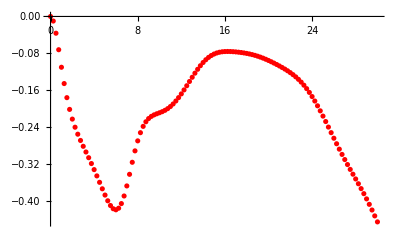

b=0.5, θA=(3 π)/4, θB=π/4

{{0.,{0.,0.}},{0.25,{-0.00989673,5.35092×10^-8}},{0.5,{-0.0362888,4.27214×10^-8}},{0.75,{-0.0720235,2.7459×10^-9}},{1.,{-0.109958,6.74367×10^-8}},{1.25,{-0.145268,7.02418×10^-8}},{1.5,{-0.175786,-1.37217×10^-8}},{1.75,{-0.201215,4.15463×10^-8}},{2.,{-0.222217,5.35948×10^-8}},{2.25,{-0.239784,3.27935×10^-10}},{2.5,{-0.254909,7.40781×10^-8}},{2.75,{-0.268454,3.32127×10^-8}},{3.,{-0.281115,-3.30795×10^-9}},{3.25,{-0.293428,5.9401×10^-9}},{3.5,{-0.305787,6.94959×10^-9}},{3.75,{-0.318457,6.46722×10^-10}},{4.,{-0.33158,-1.29337×10^-8}},{4.25,{-0.345172,-1.68262×10^-8}},{4.5,{-0.35911,-8.41252×10^-9}},{4.75,{-0.373101,-3.98326×10^-8}},{5.,{-0.386654,-3.58664×10^-8}},{5.25,{-0.399047,-1.51238×10^-8}},{5.5,{-0.40931,-7.80569×10^-9}},{5.75,{-0.416247,1.91788×10^-7}},{6.,{-0.418568,-2.50567×10^-8}},{6.25,{-0.415093,-1.67685×10^-8}},{6.5,{-0.405101,-3.91147×10^-8}},{6.75,{-0.388675,1.58792×10^-8}},{7.,{-0.366902,-1.6984×10^-8}},{7.25,{-0.341765,-1.82096×10^-7}},{7.5,{-0.315697,1.8048×10^-8}},{7.75,{-0.290991,-7.34863×10^-8}},{8.,{-0.269338,-3.42192×10^-9}},{8.25,{-0.251612,2.17781×10^-9}},{8.5,{-0.237956,1.51674×10^-7}},{8.75,{-0.22799,6.43661×10^-8}},{9.,{-0.221039,2.70005×10^-7}},{9.25,{-0.216329,2.8686×10^-7}},{9.5,{-0.2131,4.1562×10^-8}},{9.75,{-0.210677,7.99026×10^-8}},{10.,{-0.208499,5.83934×10^-8}},{10.25,{-0.206121,-6.49498×10^-8}},{10.5,{-0.203213,-1.16729×10^-7}},{10.75,{-0.199546,3.94917×10^-8}},{11.,{-0.194986,-7.04128×10^-8}},{11.25,{-0.189475,-4.0441×10^-8}},{11.5,{-0.183028,-5.69383×10^-8}},{11.75,{-0.175716,-9.59555×10^-8}},{12.,{-0.167661,-1.24251×10^-7}},{12.25,{-0.159026,-1.35833×10^-7}},{12.5,{-0.150003,-2.48021×10^-6}},{12.75,{-0.140806,-6.3412×10^-8}},{13.,{-0.131657,-1.06723×10^-7}},{13.25,{-0.122779,-1.54162×10^-7}},{13.5,{-0.11438,-7.7312×10^-8}},{13.75,{-0.106643,-8.55696×10^-8}},{14.,{-0.0997155,-8.04299×10^-8}},{14.25,{-0.0936996,-8.59868×10^-8}},{14.5,{-0.0886488,-7.9733×10^-8}},{14.75,{-0.0845648,8.66211×10^-8}},{15.,{-0.0814026,5.45163×10^-9}},{15.25,{-0.0790776,-3.65149×10^-8}},{15.5,{-0.0774803,3.78437×10^-8}},{15.75,{-0.0764858,1.2283×10^-7}},{16.,{-0.0759712,1.58107×10^-7}},{16.25,{-0.0758228,1.64572×10^-7}},{16.5,{-0.0759471,-8.08392×10^-7}},{16.75,{-0.0762731,1.849×10^-7}},{17.,{-0.076755,5.31105×10^-8}},{17.25,{-0.0773682,-5.5975×10^-8}},{17.5,{-0.0781073,8.42183×10^-8}},{17.75,{-0.0789801,4.25846×10^-7}},{18.,{-0.0800028,-9.16292×10^-8}},{18.25,{-0.0811961,-1.25579×10^-7}},{18.5,{-0.0825796,-2.46723×10^-7}},{18.75,{-0.0841673,-9.05667×10^-8}},{19.,{-0.0859699,-1.26853×10^-7}},{19.25,{-0.0879934,-3.46351×10^-6}},{19.5,{-0.0902257,-1.56371×10^-7}},{19.75,{-0.0926575,-1.15101×10^-7}},{20.,{-0.0952677,-4.32249×10^-7}},{20.25,{-0.0980366,-4.10842×10^-7}},{20.5,{-0.100946,-2.16995×10^-7}},{20.75,{-0.103984,-2.186×10^-7}},{21.,{-0.107149,-1.21806×10^-7}},{21.25,{-0.110455,-1.73187×10^-7}},{21.5,{-0.113932,-4.36645×10^-8}},{21.75,{-0.117632,-1.00437×10^-7}},{22.,{-0.12162,-7.81162×10^-8}},{22.25,{-0.125977,1.4514×10^-7}},{22.5,{-0.130793,3.25559×10^-7}},{22.75,{-0.136154,6.26698×10^-7}},{23.,{-0.142145,3.31351×10^-7}},{23.25,{-0.14883,4.37981×10^-7}},{23.5,{-0.156258,6.15125×10^-7}},{23.75,{-0.16445,1.21129×10^-6}},{24.,{-0.173401,4.82795×10^-7}},{24.25,{-0.183078,6.09674×10^-7}},{24.5,{-0.19342,2.18549×10^-7}},{24.75,{-0.204341,2.21338×10^-7}},{25.,{-0.215741,2.8364×10^-7}},{25.25,{-0.227497,-1.32649×10^-7}},{25.5,{-0.239484,-1.18856×10^-7}},{25.75,{-0.251571,-4.44845×10^-7}},{26.,{-0.263636,-3.63831×10^-7}},{26.25,{-0.275566,-5.37962×10^-8}},{26.5,{-0.287276,2.18785×10^-6}},{26.75,{-0.298701,0.0000137173}},{27.,{-0.30981,3.86072×10^-7}},{27.25,{-0.320612,3.25713×10^-6}},{27.5,{-0.331154,2.1372×10^-6}},{27.75,{-0.341512,-1.40486×10^-6}},{28.,{-0.351812,-2.16121×10^-6}},{28.25,{-0.362172,-2.31307×10^-6}},{28.5,{-0.372731,-2.55824×10^-6}},{28.75,{-0.383619,-2.58319×10^-6}},{29.,{-0.394937,-3.41008×10^-6}},{29.25,{-0.406743,-2.81256×10^-6}},{29.5,{-0.419041,-3.47758×10^-6}},{29.75,{-0.431763,-3.54052×10^-6}},{30.,{-0.444769,-2.82683×10^-6}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$74731211 near {ϕ$74731211} = {5.73085}. NIntegrate obtained -0.0000174075 and 2.79255×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$75077896 near {ϕ$75077896} = {2.27019}. NIntegrate obtained -6.7048×10^-7 and 1.24737×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$75249934 near {ϕ$75249934} = {5.70631}. NIntegrate obtained 0.0000128466 and 1.63382×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-Graphics-

b=0.5, θA=0, θB=-π/4

{{0.,{0.,0.}},{0.25,{-0.0112139,0.00584268}},{0.5,{-0.0407056,0.0245241}},{0.75,{-0.0742113,0.0542608}},{1.,{-0.09576,0.0882517}},{1.25,{-0.1,0.120056}},{1.5,{-0.0912173,0.147254}},{1.75,{-0.0757954,0.17022}},{2.,{-0.0583624,0.190019}},{2.25,{-0.0414953,0.207439}},{2.5,{-0.0264157,0.222791}},{2.75,{-0.0135933,0.235985}},{3.,{-0.00309861,0.246637}},{3.25,{0.00521327,0.254176}},{3.5,{0.0116126,0.257949}},{3.75,{0.016446,0.257324}},{4.,{0.0201021,0.251803}},{4.25,{0.0229785,0.241133}},{4.5,{0.0254458,0.225391}},{4.75,{0.0278109,0.205032}},{5.,{0.0302855,0.180878}},{5.25,{0.032968,0.154042}},{5.5,{0.0358413,0.12582}},{5.75,{0.0387878,0.0975503}},{6.,{0.0416173,0.0704962}},{6.25,{0.0440996,0.0457561}},{6.5,{0.045998,0.0242196}},{6.75,{0.0470971,0.0065574}},{7.,{0.0472189,-0.00675182}},{7.25,{0.0462471,-0.0153934}},{7.5,{0.0441278,-0.0191694}},{7.75,{0.040881,-0.0179685}},{8.,{0.0366047,-0.0117395}},{8.25,{0.0314803,-0.000483823}},{8.5,{0.0257737,0.0157431}},{8.75,{0.0198334,0.0368116}},{9.,{0.0140798,0.0624919}},{9.25,{0.00898108,0.0924161}},{9.5,{0.00501537,0.126051}},{9.75,{0.00261489,0.162674}},{10.,{0.00209823,0.201387}},{10.25,{0.00360239,0.241158}},{10.5,{0.00702994,0.280898}},{10.75,{0.0120283,0.319567}},{11.,{0.0180148,0.356279}},{11.25,{0.0242443,0.390377}},{11.5,{0.0299079,0.421467}},{11.75,{0.0342423,0.449396}},{12.,{0.0366277,0.474179}},{12.25,{0.036659,0.495903}},{12.5,{0.0341878,0.514627}},{12.75,{0.0293321,0.530296}},{13.,{0.0224688,0.542686}},{13.25,{0.0141811,0.551384}},{13.5,{0.00520976,0.555821}},{13.75,{-0.00363469,0.555337}},{14.,{-0.0115727,0.549279}},{14.25,{-0.0179624,0.537128}},{14.5,{-0.0223922,0.518602}},{14.75,{-0.0247474,0.493736}},{15.,{-0.0252193,0.462902}},{15.25,{-0.0242632,0.426772}},{15.5,{-0.0225081,0.38624}},{15.75,{-0.0206388,0.342318}},{16.,{-0.0192792,0.296037}},{16.25,{-0.0188979,0.248381}},{16.5,{-0.0197337,0.200246}},{16.75,{-0.021782,0.152444}},{17.,{-0.0248079,0.10571}},{17.25,{-0.0283856,0.0607265}},{17.5,{-0.0319754,0.0181448}},{17.75,{-0.0350003,-0.0214295}},{18.,{-0.036929,-0.0574265}},{18.25,{-0.0373469,-0.0893504}},{18.5,{-0.0360087,-0.1168}},{18.75,{-0.0328512,-0.139475}},{19.,{-0.0279891,-0.157257}},{19.25,{-0.0216813,-0.170073}},{19.5,{-0.0142895,-0.177996}},{19.75,{-0.00622847,-0.181178}},{20.,{0.00207565,-0.179826}},{20.25,{0.0102216,-0.174191}},{20.5,{0.0178561,-0.164534}},{20.75,{0.024694,-0.151144}},{21.,{0.0305214,-0.13431}},{21.25,{0.0352031,-0.114352}},{21.5,{0.0386785,-0.0916179}},{21.75,{0.040961,-0.0665119}},{22.,{0.0421237,-0.0394972}},{22.25,{0.0423013,-0.0111206}},{22.5,{0.041659,0.0179988}},{22.75,{0.0403847,0.0471733}},{23.,{0.038653,0.075708}},{23.25,{0.0366112,0.102901}},{23.5,{0.0343396,0.128156}},{23.75,{0.0318477,0.151032}},{24.,{0.0290547,0.171281}},{24.25,{0.0257997,0.188893}},{24.5,{0.0218884,0.204074}},{24.75,{0.0171128,0.217211}},{25.,{0.0113013,0.228786}},{25.25,{0.00436995,0.239297}},{25.5,{-0.00362143,0.249153}},{25.75,{-0.0124663,0.2586}},{26.,{-0.021756,0.267639}},{26.25,{-0.0309263,0.276}},{26.5,{-0.0392622,0.283126}},{26.75,{-0.0459923,0.288234}},{27.,{-0.0504096,0.290413}},{27.25,{-0.0519592,0.288762}},{27.5,{-0.0503835,0.282555}},{27.75,{-0.0457838,0.271389}},{28.,{-0.0386206,0.255254}},{28.25,{-0.0296431,0.234554}},{28.5,{-0.0197546,0.209968}},{28.75,{-0.00988171,0.182428}},{29.,{-0.000847269,0.152889}},{29.25,{0.00672039,0.122264}},{29.5,{0.0124078,0.0913463}},{29.75,{0.01604,0.0607773}},{30.,{0.0176456,0.0310573}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81977184 near {ϕ$81977184} = {3.76736}. NIntegrate obtained -1.01011×10^-9 and 2.6963×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82040704 near {ϕ$82040704} = {3.91462}. NIntegrate obtained -1.47201×10^-8 and 3.35601×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82164009 near {ϕ$82164009} = {2.57699}. NIntegrate obtained 1.48683×10^-9 and 7.28911×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-Graphics-

b=0.5, θA=π/4, θB=-π/4

{{0.,{0.,0.}},{0.25,{-0.00989673,-5.35092×10^-8}},{0.5,{-0.0362888,-4.27214×10^-8}},{0.75,{-0.0720235,-2.7459×10^-9}},{1.,{-0.109958,-6.74367×10^-8}},{1.25,{-0.145268,-7.02418×10^-8}},{1.5,{-0.175786,1.37217×10^-8}},{1.75,{-0.201215,-4.15463×10^-8}},{2.,{-0.222217,-5.35948×10^-8}},{2.25,{-0.239784,-3.27935×10^-10}},{2.5,{-0.254909,-7.46114×10^-8}},{2.75,{-0.268454,-3.32127×10^-8}},{3.,{-0.281115,3.30795×10^-9}},{3.25,{-0.293428,-5.9401×10^-9}},{3.5,{-0.305787,-6.94959×10^-9}},{3.75,{-0.318457,-6.46722×10^-10}},{4.,{-0.33158,1.29337×10^-8}},{4.25,{-0.345172,1.68262×10^-8}},{4.5,{-0.35911,8.41252×10^-9}},{4.75,{-0.373101,3.98326×10^-8}},{5.,{-0.386654,3.58664×10^-8}},{5.25,{-0.399047,1.51238×10^-8}},{5.5,{-0.40931,7.80569×10^-9}},{5.75,{-0.416247,-1.91788×10^-7}},{6.,{-0.418568,2.50567×10^-8}},{6.25,{-0.415093,1.67685×10^-8}},{6.5,{-0.405101,3.91147×10^-8}},{6.75,{-0.388675,-1.58792×10^-8}},{7.,{-0.366902,1.67912×10^-8}},{7.25,{-0.341765,1.82096×10^-7}},{7.5,{-0.315697,-1.8048×10^-8}},{7.75,{-0.290991,7.34863×10^-8}},{8.,{-0.269338,3.42192×10^-9}},{8.25,{-0.251612,-2.17781×10^-9}},{8.5,{-0.237956,-1.51556×10^-7}},{8.75,{-0.22799,-6.43661×10^-8}},{9.,{-0.221039,-2.69803×10^-7}},{9.25,{-0.216329,-2.89736×10^-7}},{9.5,{-0.2131,-4.24815×10^-8}},{9.75,{-0.210677,-7.88838×10^-8}},{10.,{-0.208499,-5.48362×10^-8}},{10.25,{-0.206121,6.51279×10^-8}},{10.5,{-0.203213,1.16729×10^-7}},{10.75,{-0.199546,-3.92766×10^-8}},{11.,{-0.194986,7.04417×10^-8}},{11.25,{-0.189475,4.17353×10^-8}},{11.5,{-0.183028,5.58341×10^-8}},{11.75,{-0.175716,9.74706×10^-8}},{12.,{-0.167661,1.24251×10^-7}},{12.25,{-0.159026,1.374×10^-7}},{12.5,{-0.150003,2.48023×10^-6}},{12.75,{-0.140806,6.3412×10^-8}},{13.,{-0.131657,1.06098×10^-7}},{13.25,{-0.122779,1.54162×10^-7}},{13.5,{-0.11438,7.7312×10^-8}},{13.75,{-0.106643,8.55696×10^-8}},{14.,{-0.0997155,8.04299×10^-8}},{14.25,{-0.0936996,8.59868×10^-8}},{14.5,{-0.0886488,1.17575×10^-7}},{14.75,{-0.0845648,-8.66211×10^-8}},{15.,{-0.0814026,-1.88783×10^-9}},{15.25,{-0.0790776,3.65149×10^-8}},{15.5,{-0.0774803,-3.78437×10^-8}},{15.75,{-0.0764858,-1.2283×10^-7}},{16.,{-0.0759712,-1.58107×10^-7}},{16.25,{-0.0758228,-1.64223×10^-7}},{16.5,{-0.0759471,8.08392×10^-7}},{16.75,{-0.0762731,-2.15967×10^-7}},{17.,{-0.076755,-5.31105×10^-8}},{17.25,{-0.0773682,5.55009×10^-8}},{17.5,{-0.0781073,-8.42183×10^-8}},{17.75,{-0.0789801,-4.25846×10^-7}},{18.,{-0.0800028,9.16292×10^-8}},{18.25,{-0.0811961,1.25579×10^-7}},{18.5,{-0.0825796,2.46723×10^-7}},{18.75,{-0.0841673,9.05667×10^-8}},{19.,{-0.0859699,1.53454×10^-7}},{19.25,{-0.0879934,3.46351×10^-6}},{19.5,{-0.0902257,1.58614×10^-7}},{19.75,{-0.0926575,9.58662×10^-8}},{20.,{-0.0952677,4.32249×10^-7}},{20.25,{-0.0980366,4.19384×10^-7}},{20.5,{-0.100946,2.27593×10^-7}},{20.75,{-0.103984,2.186×10^-7}},{21.,{-0.107149,1.21806×10^-7}},{21.25,{-0.110455,1.73186×10^-7}},{21.5,{-0.113932,2.5956×10^-8}},{21.75,{-0.117632,8.92504×10^-8}},{22.,{-0.12162,7.81162×10^-8}},{22.25,{-0.125977,-1.4514×10^-7}},{22.5,{-0.130793,-3.25559×10^-7}},{22.75,{-0.136154,-6.11467×10^-7}},{23.,{-0.142145,-3.31351×10^-7}},{23.25,{-0.14883,-4.37981×10^-7}},{23.5,{-0.156258,-6.15125×10^-7}},{23.75,{-0.164451,-1.21129×10^-6}},{24.,{-0.173401,-5.04627×10^-7}},{24.25,{-0.183078,-6.09674×10^-7}},{24.5,{-0.19342,-1.82139×10^-7}},{24.75,{-0.204341,-2.21338×10^-7}},{25.,{-0.215741,-2.85994×10^-7}},{25.25,{-0.227497,1.32649×10^-7}},{25.5,{-0.239484,1.12628×10^-7}},{25.75,{-0.251571,4.44845×10^-7}},{26.,{-0.263636,3.63831×10^-7}},{26.25,{-0.275566,5.37962×10^-8}},{26.5,{-0.287276,-2.18785×10^-6}},{26.75,{-0.298701,-0.0000137173}},{27.,{-0.30981,-3.86072×10^-7}},{27.25,{-0.320612,-3.26413×10^-6}},{27.5,{-0.331154,-2.1372×10^-6}},{27.75,{-0.341512,1.40486×10^-6}},{28.,{-0.351812,2.16121×10^-6}},{28.25,{-0.362172,2.31307×10^-6}},{28.5,{-0.372731,2.55824×10^-6}},{28.75,{-0.383619,2.57837×10^-6}},{29.,{-0.394937,3.41008×10^-6}},{29.25,{-0.406743,2.81256×10^-6}},{29.5,{-0.419041,3.48285×10^-6}},{29.75,{-0.431763,3.54052×10^-6}},{30.,{-0.444769,2.83943×10^-6}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$90745975 near {ϕ$90745975} = {4.28278}. NIntegrate obtained 4.77966×10^-6 and 7.60031×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$91601965 near {ϕ$91601965} = {1.86522}. NIntegrate obtained 3.50728×10^-6 and 6.20202×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$91676525 near {ϕ$91676525} = {0.108492}. NIntegrate obtained -3.54075×10^-6 and 6.35772×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

b=0.5, θA=π/2, θB=-π/4

{{0.,{0.,0.}},{0.25,{-0.00309306,-0.000750924}},{0.5,{-0.0119145,-0.00323078}},{0.75,{-0.0251503,-0.00778635}},{1.,{-0.0407959,-0.0146037}},{1.25,{-0.0564838,-0.0236247}},{1.5,{-0.0698936,-0.0345615}},{1.75,{-0.0791022,-0.0469708}},{2.,{-0.0827828,-0.0603467}},{2.25,{-0.0802443,-0.0741944}},{2.5,{-0.0713666,-0.0880695}},{2.75,{-0.0564957,-0.101583}},{3.,{-0.0363526,-0.114382}},{3.25,{-0.0119738,-0.126112}},{3.5,{0.0153098,-0.136383}},{3.75,{0.0438767,-0.14473}},{4.,{0.0718236,-0.150591}},{4.25,{0.097015,-0.153302}},{4.5,{0.117202,-0.152123}},{4.75,{0.130237,-0.1463}},{5.,{0.134382,-0.135169}},{5.25,{0.128652,-0.118277}},{5.5,{0.113128,-0.09551}},{5.75,{0.0890951,-0.067164}},{6.,{0.0589674,-0.0339598}},{6.25,{0.0259637,0.00303085}},{6.5,{-0.00636043,0.0425092}},{6.75,{-0.0346051,0.0830886}},{7.,{-0.0559293,0.123408}},{7.25,{-0.0683078,0.1622}},{7.5,{-0.0706468,0.198316}},{7.75,{-0.0627977,0.230726}},{8.,{-0.0455087,0.25852}},{8.25,{-0.0203369,0.28091}},{8.5,{0.0104769,0.297281}},{8.75,{0.0441865,0.307251}},{9.,{0.0777857,0.31074}},{9.25,{0.10831,0.308032}},{9.5,{0.133165,0.299786}},{9.75,{0.150415,0.286994}},{10.,{0.158979,0.270877}},{10.25,{0.158677,0.252753}},{10.5,{0.150148,0.233892}},{10.75,{0.134649,0.215387}},{11.,{0.113818,0.198094}},{11.25,{0.0898225,0.183391}},{11.5,{0.0632308,0.16921}},{11.75,{0.0367768,0.158039}},{12.,{0.0113943,0.149014}},{12.25,{-0.0118614,0.141936}},{12.5,{-0.0321957,0.136534}},{12.75,{-0.0490541,0.132495}},{13.,{-0.0620967,0.129492}},{13.25,{-0.0711708,0.127212}},{13.5,{-0.0762895,0.125364}},{13.75,{-0.0776124,0.123699}},{14.,{-0.0754321,0.122011}},{14.25,{-0.0701608,0.120151}},{14.5,{-0.062317,0.118024}},{14.75,{-0.0525102,0.115598}},{15.,{-0.0414184,0.112896}},{15.25,{-0.0297618,0.10999}},{15.5,{-0.0182675,0.106998}},{15.75,{-0.00763215,0.104063}},{16.,{0.00151987,0.101344}},{16.25,{0.00867468,0.0989935}},{16.5,{0.0134628,0.0971424}},{16.75,{0.0156783,0.0958867}},{17.,{0.0152882,0.0952769}},{17.25,{0.0124257,0.0953124}},{17.5,{0.00736881,0.0959467}},{17.75,{0.000509033,0.097091}},{18.,{-0.00768344,0.0986267}},{18.25,{-0.0166996,0.100421}},{18.5,{-0.0260283,0.102337}},{18.75,{-0.0351844,0.104249}},{19.,{-0.0437342,0.106056}},{19.25,{-0.0513119,0.107684}},{19.5,{-0.0576253,0.109106}},{19.75,{-0.0624679,0.110312}},{20.,{-0.0657111,0.111344}},{20.25,{-0.0673042,0.112276}},{20.5,{-0.0672706,0.113214}},{20.75,{-0.0657012,0.114286}},{21.,{-0.0627482,0.115639}},{21.25,{-0.0586199,0.117428}},{21.5,{-0.0535725,0.119806}},{21.75,{-0.0479014,0.122912}},{22.,{-0.0419305,0.126864}},{22.25,{-0.0359997,0.131744}},{22.5,{-0.0304498,0.137592}},{22.75,{-0.0256034,0.144396}},{23.,{-0.0217452,0.152089}},{23.25,{-0.0191022,0.160551}},{23.5,{-0.0178262,0.169621}},{23.75,{-0.0179816,0.179099}},{24.,{-0.0195381,0.188773}},{24.25,{-0.0223733,0.198431}},{24.5,{-0.0262844,0.207883}},{24.75,{-0.0310009,0.216981}},{25.,{-0.036211,0.225623}},{25.25,{-0.0415842,0.233765}},{25.5,{-0.0467897,0.241423}},{25.75,{-0.0515226,0.248667}},{26.,{-0.0555143,0.255616}},{26.25,{-0.0585458,0.262415}},{26.5,{-0.0604584,0.269247}},{26.75,{-0.0611525,0.276288}},{27.,{-0.0605884,0.283729}},{27.25,{-0.0587961,0.291744}},{27.5,{-0.0558618,0.300481}},{27.75,{-0.0519364,0.310043}},{28.,{-0.0472235,0.320506}},{28.25,{-0.0419807,0.331872}},{28.5,{-0.0365045,0.344095}},{28.75,{-0.0311168,0.357059}},{29.,{-0.026146,0.370586}},{29.25,{-0.0219039,0.384445}},{29.5,{-0.018656,0.398357}},{29.75,{-0.0165994,0.412024}},{30.,{-0.0158363,0.425149}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$99433040 near {ϕ$99433040} = {1.61979}. NIntegrate obtained -7.35538×10^-6 and 1.08581×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$99723767 near {ϕ$99723767} = {4.54049}. NIntegrate obtained 0.0000247162 and 3.793×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$99834747 near {ϕ$99834747} = {2.9206}. NIntegrate obtained -5.52538×10^-7 and 2.82468×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-Graphics-

b=0.5, θA=(3 π)/4, θB=-π/4

{{0.,{0.,0.}},{0.25,{-0.00447884,0.00171949}},{0.5,{-0.0179197,0.00708555}},{0.75,{-0.0397211,0.0164856}},{1.,{-0.0680913,0.0302315}},{1.25,{-0.099895,0.0483159}},{1.5,{-0.130918,0.0701361}},{1.75,{-0.156542,0.0942516}},{2.,{-0.172676,0.11828}},{2.25,{-0.176639,0.139023}},{2.5,{-0.167754,0.152872}},{2.75,{-0.147453,0.156453}},{3.,{-0.118905,0.147393}},{3.25,{-0.0862529,0.124951}},{3.5,{-0.0536787,0.0902718}},{3.75,{-0.0245865,0.0461442}},{4.,{-0.00111986,-0.00366089}},{4.25,{0.0158991,-0.055189}},{4.5,{0.0267118,-0.104955}},{4.75,{0.0322221,-0.150306}},{5.,{0.0336128,-0.189495}},{5.25,{0.0320703,-0.221555}},{5.5,{0.0286269,-0.246106}},{5.75,{0.0240974,-0.263143}},{6.,{0.0190751,-0.272867}},{6.25,{0.013957,-0.275569}},{6.5,{0.00897689,-0.27155}},{6.75,{0.00424038,-0.261079}},{7.,{-0.000253611,-0.244383}},{7.25,{-0.00458554,-0.221654}},{7.5,{-0.00891146,-0.193081}},{7.75,{-0.0134516,-0.158896}},{8.,{-0.0184907,-0.119452}},{8.25,{-0.0243722,-0.0753187}},{8.5,{-0.0314934,-0.0274037}},{8.75,{-0.0402861,0.0229149}},{9.,{-0.0511858,0.0736715}},{9.25,{-0.0645734,0.122263}},{9.5,{-0.0807003,0.165533}},{9.75,{-0.0996002,0.200052}},{10.,{-0.121022,0.222622}},{10.25,{-0.144407,0.230905}},{10.5,{-0.16895,0.224}},{10.75,{-0.19373,0.202726}},{11.,{-0.21788,0.169478}},{11.25,{-0.240721,0.12771}},{11.5,{-0.261848,0.0812494}},{11.75,{-0.281112,0.0336838}},{12.,{-0.298571,-0.0120242}},{12.25,{-0.314399,-0.0536817}},{12.5,{-0.328805,-0.0898243}},{12.75,{-0.341967,-0.119576}},{13.,{-0.354001,-0.142497}},{13.25,{-0.364899,-0.158417}},{13.5,{-0.374536,-0.167352}},{13.75,{-0.382649,-0.169422}},{14.,{-0.388823,-0.164836}},{14.25,{-0.392495,-0.153906}},{14.5,{-0.392965,-0.13709}},{14.75,{-0.389428,-0.115068}},{15.,{-0.381037,-0.0888208}},{15.25,{-0.367012,-0.0597009}},{15.5,{-0.346783,-0.0294521}},{15.75,{-0.320162,-0.000144713}},{16.,{-0.287493,0.0260097}},{16.25,{-0.249735,0.0469509}},{16.5,{-0.208407,0.0610967}},{16.75,{-0.165403,0.0676296}},{17.,{-0.122707,0.0666488}},{17.25,{-0.0820962,0.0590808}},{17.5,{-0.044926,0.0464577}},{17.75,{-0.0120178,0.0306052}},{18.,{0.016289,0.0133627}},{18.25,{0.0400529,-0.00361791}},{18.5,{0.0595933,-0.0189896}},{18.75,{0.0753484,-0.0317408}},{19.,{0.087859,-0.0411664}},{19.25,{0.0975401,-0.046842}},{19.5,{0.104788,-0.0485788}},{19.75,{0.109905,-0.0463836}},{20.,{0.113081,-0.0404471}},{20.25,{0.114416,-0.0311371}},{20.5,{0.113907,-0.0190035}},{20.75,{0.111483,-0.00479611}},{21.,{0.107007,0.0105347}},{21.25,{0.100323,0.025842}},{21.5,{0.0912774,0.0398222}},{21.75,{0.0797814,0.0510971}},{22.,{0.0658387,0.0583395}},{22.25,{0.0495994,0.0604411}},{22.5,{0.031369,0.0566755}},{22.75,{0.0116055,0.0468488}},{23.,{-0.00914203,0.031355}},{23.25,{-0.0302548,0.0111498}},{23.5,{-0.0511538,-0.0123781}},{23.75,{-0.0713547,-0.0376014}},{24.,{-0.0904931,-0.0628242}},{24.25,{-0.108352,-0.0864554}},{24.5,{-0.124825,-0.107122}},{24.75,{-0.13991,-0.123698}},{25.,{-0.15366,-0.135312}},{25.25,{-0.166154,-0.141329}},{25.5,{-0.177456,-0.141321}},{25.75,{-0.18759,-0.135028}},{26.,{-0.196511,-0.122368}},{26.25,{-0.204084,-0.103444}},{26.5,{-0.210066,-0.0786077}},{26.75,{-0.214104,-0.0485107}},{27.,{-0.215748,-0.014199}},{27.25,{-0.214464,0.0227864}},{27.5,{-0.20973,0.0604113}},{27.75,{-0.201111,0.0961982}},{28.,{-0.188388,0.127429}},{28.25,{-0.171668,0.151501}},{28.5,{-0.15142,0.166332}},{28.75,{-0.128506,0.170779}},{29.,{-0.104017,0.164822}},{29.25,{-0.0791118,0.149541}},{29.5,{-0.0548606,0.126838}},{29.75,{-0.032092,0.0990466}},{30.,{-0.011356,0.0685415}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$107065103 near {ϕ$107065103} = {2.57699}. NIntegrate obtained 2.11636×10^-16 and 7.88951×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$107119734 near {ϕ$107119734} = {2.08612}. NIntegrate obtained -6.5269×10^-17 and 2.46088×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$107164443 near {ϕ$107164443} = {4.25823}. NIntegrate obtained -3.45015×10^-15 and 3.31756×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

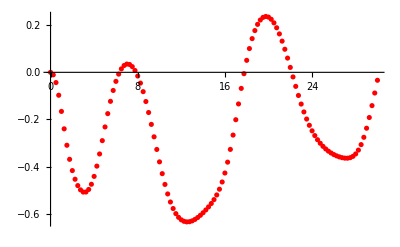

b=0.5, θA=0, θB=0

{{0.,{0.,0.}},{0.25,{-0.0106715,7.28664×10^-17}},{0.5,{-0.0434514,-9.8774×10^-17}},{0.75,{-0.0971426,-1.28713×10^-14}},{1.,{-0.165764,-1.50032×10^-13}},{1.25,{-0.239645,1.56113×10^-9}},{1.5,{-0.309323,6.25079×10^-15}},{1.75,{-0.368932,1.22877×10^-14}},{2.,{-0.416714,-5.73674×10^-17}},{2.25,{-0.453408,-1.14064×10^-11}},{2.5,{-0.480383,-4.27289×10^-9}},{2.75,{-0.498513,-8.53376×10^-17}},{3.,{-0.507813,1.90441×10^-9}},{3.25,{-0.507579,-2.86875×10^-12}},{3.5,{-0.496807,1.2099×10^-13}},{3.75,{-0.474734,-1.18308×10^-16}},{4.,{-0.441365,4.85076×10^-17}},{4.25,{-0.397795,6.34661×10^-17}},{4.5,{-0.346241,5.38103×10^-10}},{4.75,{-0.289744,1.38582×10^-9}},{5.,{-0.231672,2.5029×10^-12}},{5.25,{-0.17521,-2.57823×10^-12}},{5.5,{-0.122993,-4.49087×10^-13}},{5.75,{-0.0769421,1.73357×10^-17}},{6.,{-0.0382769,2.58386×10^-11}},{6.25,{-0.00763765,-1.5439×10^-11}},{6.5,{0.0147428,-4.4633×10^-11}},{6.75,{0.0289075,1.1097×10^-10}},{7.,{0.0350356,-3.46196×10^-8}},{7.25,{0.033373,2.45355×10^-16}},{7.5,{0.0241829,-2.14926×10^-16}},{7.75,{0.00773629,-1.82275×10^-16}},{8.,{-0.0156794,-2.26276×10^-8}},{8.25,{-0.0457249,4.24219×10^-10}},{8.5,{-0.0819639,1.34886×10^-8}},{8.75,{-0.123803,3.17056×10^-16}},{9.,{-0.170435,-1.22352×10^-16}},{9.25,{-0.220794,-3.89234×10^-11}},{9.5,{-0.273541,-6.20744×10^-9}},{9.75,{-0.327093,5.63379×10^-11}},{10.,{-0.379723,3.07022×10^-17}},{10.25,{-0.429696,-6.8197×10^-17}},{10.5,{-0.47546,-2.57448×10^-16}},{10.75,{-0.515805,-3.8489×10^-16}},{11.,{-0.549986,-2.95933×10^-16}},{11.25,{-0.577749,-3.487×10^-16}},{11.5,{-0.599273,7.46785×10^-8}},{11.75,{-0.615042,1.38991×10^-9}},{12.,{-0.625702,-8.41805×10^-16}},{12.25,{-0.631932,2.1978×10^-11}},{12.5,{-0.634356,-1.00547×10^-12}},{12.75,{-0.633515,3.3547×10^-8}},{13.,{-0.629875,6.30281×10^-11}},{13.25,{-0.623859,9.14097×10^-11}},{13.5,{-0.615871,-1.42323×10^-16}},{13.75,{-0.606298,-2.41359×10^-8}},{14.,{-0.595472,8.67014×10^-11}},{14.25,{-0.583597,-1.56931×10^-10}},{14.5,{-0.570654,3.75058×10^-16}},{14.75,{-0.556305,-4.57323×10^-8}},{15.,{-0.53982,-1.31205×10^-8}},{15.25,{-0.520077,3.01006×10^-9}},{15.5,{-0.495668,-1.12681×10^-15}},{15.75,{-0.465086,1.87164×10^-10}},{16.,{-0.427061,-8.54531×10^-17}},{16.25,{-0.38091,-3.16108×10^-9}},{16.5,{-0.326861,3.15177×10^-9}},{16.75,{-0.266169,-4.69025×10^-10}},{17.,{-0.200992,-3.91445×10^-8}},{17.25,{-0.134039,6.94083×10^-16}},{17.5,{-0.0681453,-1.32713×10^-9}},{17.75,{-0.00582474,-1.61851×10^-9}},{18.,{0.0509355,-1.61545×10^-9}},{18.25,{0.100791,-9.89269×10^-9}},{18.5,{0.142972,1.34157×10^-9}},{18.75,{0.17716,-7.36942×10^-10}},{19.,{0.203422,-9.34867×10^-10}},{19.25,{0.221928,2.03137×10^-7}},{19.5,{0.232989,8.59648×10^-9}},{19.75,{0.236958,-2.198×10^-7}},{20.,{0.234181,-1.28083×10^-8}},{20.25,{0.225013,4.57779×10^-9}},{20.5,{0.209807,4.41739×10^-9}},{20.75,{0.188965,-6.07709×10^-9}},{21.,{0.162951,-1.44002×10^-9}},{21.25,{0.132343,-3.16912×10^-15}},{21.5,{0.0978453,-2.46617×10^-9}},{21.75,{0.0603548,-5.4368×10^-15}},{22.,{0.0208642,5.75727×10^-9}},{22.25,{-0.0194758,6.55337×10^-9}},{22.5,{-0.0595225,7.07665×10^-9}},{22.75,{-0.0981815,1.55205×10^-15}},{23.,{-0.134563,5.19663×10^-9}},{23.25,{-0.167978,1.92995×10^-10}},{23.5,{-0.198057,1.95048×10^-9}},{23.75,{-0.224699,-2.16751×10^-9}},{24.,{-0.248018,2.70236×10^-16}},{24.25,{-0.268272,6.18513×10^-9}},{24.5,{-0.285796,-2.69364×10^-9}},{24.75,{-0.300898,4.52237×10^-8}},{25.,{-0.313859,5.74688×10^-8}},{25.25,{-0.324955,7.99537×10^-10}},{25.5,{-0.334358,7.7437×10^-8}},{25.75,{-0.342254,4.66699×10^-9}},{26.,{-0.348852,9.76381×10^-8}},{26.25,{-0.354268,1.0625×10^-7}},{26.5,{-0.358613,1.04565×10^-7}},{26.75,{-0.36187,-1.78241×10^-8}},{27.,{-0.363853,3.64496×10^-9}},{27.25,{-0.364125,-1.4817×10^-9}},{27.5,{-0.361962,1.04858×10^-8}},{27.75,{-0.356355,-2.431×10^-9}},{28.,{-0.346072,-1.1008×10^-8}},{28.25,{-0.32985,-2.31622×10^-8}},{28.5,{-0.306568,1.60665×10^-9}},{28.75,{-0.275601,4.12999×10^-9}},{29.,{-0.237011,7.33871×10^-9}},{29.25,{-0.191661,1.07229×10^-8}},{29.5,{-0.141195,-2.05186×10^-8}},{29.75,{-0.0877494,-1.10663×10^-8}},{30.,{-0.0336855,-1.49496×10^-8}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$116326871 near {ϕ$116326871} = {2.15975}. NIntegrate obtained 0.0000174077 and 1.87579×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$116658982 near {ϕ$116658982} = {0.883475}. NIntegrate obtained 6.70484×10^-7 and 5.55886×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$116962990 near {ϕ$116962990} = {6.19219512839554360461580273522486095316708087921142578125}. NIntegrate obtained 3.43458×10^-6 and 4.30308×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

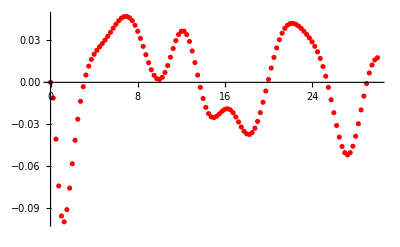

b=0.5, θA=π/4, θB=0

{{0.,{0.,0.}},{0.25,{-0.0112143,-0.00584256}},{0.5,{-0.0407058,-0.0245241}},{0.75,{-0.0742112,-0.0542609}},{1.,{-0.0957601,-0.0882517}},{1.25,{-0.1,-0.120056}},{1.5,{-0.0912174,-0.147254}},{1.75,{-0.0757954,-0.17022}},{2.,{-0.0583624,-0.190019}},{2.25,{-0.0414952,-0.207439}},{2.5,{-0.0264158,-0.222792}},{2.75,{-0.0135932,-0.235985}},{3.,{-0.00309863,-0.246637}},{3.25,{0.00521328,-0.254176}},{3.5,{0.0116126,-0.257949}},{3.75,{0.016446,-0.257324}},{4.,{0.0201021,-0.251803}},{4.25,{0.0229785,-0.241133}},{4.5,{0.0254458,-0.225391}},{4.75,{0.0278109,-0.205032}},{5.,{0.0302855,-0.180878}},{5.25,{0.032968,-0.154042}},{5.5,{0.0358413,-0.125821}},{5.75,{0.0387878,-0.0975502}},{6.,{0.0416172,-0.0704962}},{6.25,{0.0440997,-0.0457562}},{6.5,{0.045998,-0.0242196}},{6.75,{0.047097,-0.00655743}},{7.,{0.0472188,0.0067519}},{7.25,{0.046247,0.0153934}},{7.5,{0.0441278,0.0191694}},{7.75,{0.0408809,0.0179685}},{8.,{0.0366047,0.0117394}},{8.25,{0.0314802,0.000483826}},{8.5,{0.0257737,-0.0157431}},{8.75,{0.0198335,-0.0368114}},{9.,{0.0140799,-0.0624917}},{9.25,{0.00898101,-0.092416}},{9.5,{0.00501544,-0.126051}},{9.75,{0.00261498,-0.162673}},{10.,{0.00209828,-0.201387}},{10.25,{0.0036026,-0.241157}},{10.5,{0.00702994,-0.280898}},{10.75,{0.0120284,-0.319567}},{11.,{0.018015,-0.356279}},{11.25,{0.0242441,-0.390377}},{11.5,{0.0299077,-0.421467}},{11.75,{0.0342422,-0.449396}},{12.,{0.0366275,-0.474179}},{12.25,{0.0366589,-0.495903}},{12.5,{0.0341876,-0.514627}},{12.75,{0.0293316,-0.530296}},{13.,{0.0224683,-0.542686}},{13.25,{0.0141807,-0.551385}},{13.5,{0.00520926,-0.555821}},{13.75,{-0.00363508,-0.555336}},{14.,{-0.0115736,-0.549279}},{14.25,{-0.017963,-0.537128}},{14.5,{-0.0223926,-0.518603}},{14.75,{-0.0247477,-0.493736}},{15.,{-0.0252195,-0.462902}},{15.25,{-0.0242634,-0.426771}},{15.5,{-0.0225083,-0.38624}},{15.75,{-0.0206392,-0.342318}},{16.,{-0.0192807,-0.296038}},{16.25,{-0.0188975,-0.248381}},{16.5,{-0.0197358,-0.200246}},{16.75,{-0.0217833,-0.152445}},{17.,{-0.0248076,-0.10571}},{17.25,{-0.0283861,-0.060726}},{17.5,{-0.031977,-0.0181422}},{17.75,{-0.0350015,0.0214313}},{18.,{-0.0369287,0.0574271}},{18.25,{-0.0373461,0.0893513}},{18.5,{-0.0360078,0.1168}},{18.75,{-0.0328504,0.139476}},{19.,{-0.0279877,0.157258}},{19.25,{-0.0216806,0.170076}},{19.5,{-0.0142873,0.177998}},{19.75,{-0.00622671,0.181179}},{20.,{0.00207755,0.179826}},{20.25,{0.0102235,0.174192}},{20.5,{0.0178582,0.164535}},{20.75,{0.024696,0.151145}},{21.,{0.0305233,0.134311}},{21.25,{0.0352052,0.114353}},{21.5,{0.038682,0.0916186}},{21.75,{0.0409635,0.0665133}},{22.,{0.0421273,0.0394981}},{22.25,{0.0423051,0.0111223}},{22.5,{0.0416635,-0.0179975}},{22.75,{0.0403889,-0.047173}},{23.,{0.0386582,-0.0757069}},{23.25,{0.0366151,-0.102901}},{23.5,{0.0343461,-0.128164}},{23.75,{0.031851,-0.151031}},{24.,{0.029058,-0.171279}},{24.25,{0.0258016,-0.18889}},{24.5,{0.0218911,-0.204071}},{24.75,{0.0171138,-0.217207}},{25.,{0.011303,-0.228782}},{25.25,{0.004372,-0.239292}},{25.5,{-0.00362174,-0.249149}},{25.75,{-0.0124635,-0.258596}},{26.,{-0.0217539,-0.267634}},{26.25,{-0.030923,-0.275995}},{26.5,{-0.0392559,-0.28312}},{26.75,{-0.0459861,-0.288227}},{27.,{-0.050406,-0.290408}},{27.25,{-0.0519525,-0.288756}},{27.5,{-0.0503737,-0.28255}},{27.75,{-0.0457735,-0.271381}},{28.,{-0.0386101,-0.255248}},{28.25,{-0.0296329,-0.234537}},{28.5,{-0.019741,-0.20996}},{28.75,{-0.00987003,-0.182421}},{29.,{-0.000835335,-0.152883}},{29.25,{0.00673058,-0.122258}},{29.5,{0.0124157,-0.0913389}},{29.75,{0.0160513,-0.0607658}},{30.,{0.0176557,-0.0310425}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$123926429 near {ϕ$123926429} = {1.10437}. NIntegrate obtained -1.04422×10^-14 and 3.06277×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$123998805 near {ϕ$123998805} = {2.03703}. NIntegrate obtained -8.2356×10^-16 and 1.39253×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$124048467 near {ϕ$124048467} = {0.957106}. NIntegrate obtained 3.26667×10^-15 and 2.34247×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

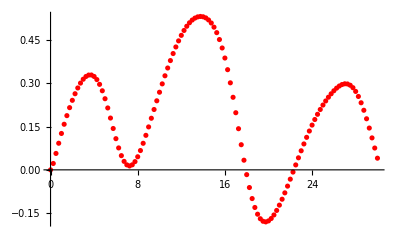

b=0.5, θA=π/2, θB=0

{{0.,{0.,0.}},{0.25,{0.0221791,-3.57969×10^-13}},{0.5,{0.0570198,-2.53689×10^-14}},{0.75,{0.0924469,9.51737×10^-14}},{1.,{0.126369,2.36809×10^-13}},{1.25,{0.158359,-1.2185×10^-12}},{1.5,{0.188286,5.42911×10^-13}},{1.75,{0.216041,-1.191×10^-16}},{2.,{0.241466,6.46678×10^-12}},{2.25,{0.264347,-2.31687×10^-12}},{2.5,{0.284411,-1.60028×10^-12}},{2.75,{0.301331,-3.25384×10^-12}},{3.,{0.314724,7.31139×10^-15}},{3.25,{0.324169,5.65814×10^-9}},{3.5,{0.32921,6.04338×10^-17}},{3.75,{0.329386,8.21344×10^-10}},{4.,{0.324269,-1.14246×10^-11}},{4.25,{0.313515,1.23706×10^-17}},{4.5,{0.296944,-1.50974×10^-9}},{4.75,{0.274634,-2.5873×10^-11}},{5.,{0.247021,1.57885×10^-11}},{5.25,{0.214987,2.27064×10^-9}},{5.5,{0.179908,2.07395×10^-16}},{5.75,{0.143619,1.95844×10^-9}},{6.,{0.108286,-1.0744×10^-8}},{6.25,{0.0761717,3.26025×10^-10}},{6.5,{0.049352,2.41255×10^-10}},{6.75,{0.0294468,-4.45045×10^-12}},{7.,{0.0174349,-4.98876×10^-9}},{7.25,{0.0135951,1.41542×10^-8}},{7.5,{0.0175804,2.47087×10^-8}},{7.75,{0.0285727,6.61884×10^-12}},{8.,{0.0454757,-1.13674×10^-10}},{8.25,{0.0670883,-3.22247×10^-11}},{8.5,{0.0922416,-2.27135×10^-10}},{8.75,{0.119882,6.78219×10^-11}},{9.,{0.149113,-1.87157×10^-10}},{9.25,{0.179206,-3.47191×10^-10}},{9.5,{0.209589,2.81011×10^-11}},{9.75,{0.239822,8.48787×10^-9}},{10.,{0.269576,2.42953×10^-10}},{10.25,{0.2986,-2.42247×10^-11}},{10.5,{0.326704,1.56678×10^-10}},{10.75,{0.353726,2.36032×10^-9}},{11.,{0.379522,3.15763×10^-10}},{11.25,{0.403939,4.02906×10^-10}},{11.5,{0.42681,7.8517×10^-11}},{11.75,{0.447941,1.70031×10^-7}},{12.,{0.467118,1.62748×10^-10}},{12.25,{0.484116,3.86989×10^-10}},{12.5,{0.498729,-2.47109×10^-10}},{12.75,{0.510796,3.23926×10^-8}},{13.,{0.52023,-1.30043×10^-9}},{13.25,{0.527012,-4.62571×10^-10}},{13.5,{0.531167,4.03013×10^-10}},{13.75,{0.532708,-3.03598×10^-9}},{14.,{0.531582,-3.12204×10^-9}},{14.25,{0.527633,-1.57338×10^-9}},{14.5,{0.520575,-1.63879×10^-9}},{14.75,{0.510019,-4.35859×10^-10}},{15.,{0.495496,4.42026×10^-10}},{15.25,{0.476498,1.65237×10^-9}},{15.5,{0.452544,3.77151×10^-9}},{15.75,{0.423239,1.3066×10^-9}},{16.,{0.38835,3.12556×10^-7}},{16.25,{0.34789,1.44509×10^-10}},{16.5,{0.302197,-7.05844×10^-8}},{16.75,{0.251987,1.49791×10^-9}},{17.,{0.198388,1.45253×10^-9}},{17.25,{0.142898,-4.99474×10^-8}},{17.5,{0.0873048,3.77194×10^-8}},{17.75,{0.0335189,2.60807×10^-9}},{18.,{-0.0165959,2.47272×10^-9}},{18.25,{-0.0614165,4.35997×10^-9}},{18.5,{-0.0996976,8.77618×10^-11}},{18.75,{-0.130643,5.22678×10^-10}},{19.,{-0.153979,2.61852×10^-9}},{19.25,{-0.16978,3.82922×10^-11}},{19.5,{-0.178478,-5.93258×10^-9}},{19.75,{-0.18073,-1.03881×10^-9}},{20.,{-0.177303,1.24235×10^-9}},{20.25,{-0.169014,-4.7673×10^-9}},{20.5,{-0.156644,9.27972×10^-10}},{20.75,{-0.140923,-4.26911×10^-9}},{21.,{-0.122525,-3.53607×10^-9}},{21.25,{-0.102002,-3.98041×10^-9}},{21.5,{-0.079854,-2.27653×10^-10}},{21.75,{-0.056513,-3.88586×10^-10}},{22.,{-0.0323489,5.8676×10^-9}},{22.25,{-0.00770064,8.99237×10^-9}},{22.5,{0.0171334,1.20071×10^-9}},{22.75,{0.0418629,1.16153×10^-8}},{23.,{0.0662368,6.70043×10^-9}},{23.25,{0.0899907,6.14339×10^-8}},{23.5,{0.112904,5.61242×10^-9}},{23.75,{0.134778,7.11743×10^-8}},{24.,{0.155463,1.4345×10^-8}},{24.25,{0.174854,-1.60054×10^-7}},{24.5,{0.192905,4.73071×10^-9}},{24.75,{0.209626,9.89867×10^-9}},{25.,{0.22506,5.40521×10^-9}},{25.25,{0.239267,1.42122×10^-8}},{25.5,{0.25229,7.81366×10^-10}},{25.75,{0.264122,7.13392×10^-9}},{26.,{0.274682,3.18021×10^-8}},{26.25,{0.28378,-1.06473×10^-9}},{26.5,{0.291121,7.5423×10^-7}},{26.75,{0.296298,1.41691×10^-8}},{27.,{0.298827,-1.80538×10^-8}},{27.25,{0.298178,-1.17684×10^-8}},{27.5,{0.293828,-3.37492×10^-9}},{27.75,{0.285337,-1.92719×10^-8}},{28.,{0.272387,-1.48398×10^-8}},{28.25,{0.254884,1.34804×10^-8}},{28.5,{0.232949,7.28406×10^-7}},{28.75,{0.206933,6.44597×10^-9}},{29.,{0.177421,5.8189×10^-8}},{29.25,{0.145153,-1.23905×10^-8}},{29.5,{0.110991,2.7053×10^-8}},{29.75,{0.0758283,3.27654×10^-8}},{30.,{0.0405319,2.86157×10^-8}}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$132717636 near {ϕ$132717636} = {4.13551}. NIntegrate obtained -0.0000174077 and 1.87579×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$133049817 near {ϕ$133049817} = {5.41179}. NIntegrate obtained -6.70484×10^-7 and 5.55886×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$133353326 near {ϕ$133353326} = {0.0909902}. NIntegrate obtained 3.43458×10^-6 and 4.30308×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-Graphics-

b=0.5, θA=(3 π)/4, θB=0

{{0.,{0.,0.}},{0.25,{-0.0112143,0.00584256}},{0.5,{-0.0407058,0.0245241}},{0.75,{-0.0742112,0.0542609}},{1.,{-0.0957601,0.0882517}},{1.25,{-0.1,0.120056}},{1.5,{-0.0912174,0.147254}},{1.75,{-0.0757954,0.17022}},{2.,{-0.0583624,0.190019}},{2.25,{-0.0414952,0.207439}},{2.5,{-0.0264158,0.222792}},{2.75,{-0.0135932,0.235985}},{3.,{-0.00309863,0.246637}},{3.25,{0.00521328,0.254176}},{3.5,{0.0116126,0.257949}},{3.75,{0.016446,0.257324}},{4.,{0.0201021,0.251803}},{4.25,{0.0229785,0.241133}},{4.5,{0.0254458,0.225391}},{4.75,{0.0278109,0.205032}},{5.,{0.0302855,0.180878}},{5.25,{0.032968,0.154042}},{5.5,{0.0358413,0.125821}},{5.75,{0.0387878,0.0975502}},{6.,{0.0416172,0.0704962}},{6.25,{0.0440997,0.0457562}},{6.5,{0.045998,0.0242196}},{6.75,{0.047097,0.00655743}},{7.,{0.0472188,-0.0067519}},{7.25,{0.046247,-0.0153934}},{7.5,{0.0441278,-0.0191694}},{7.75,{0.0408809,-0.0179685}},{8.,{0.0366047,-0.0117394}},{8.25,{0.0314802,-0.000483826}},{8.5,{0.0257737,0.0157431}},{8.75,{0.0198335,0.0368114}},{9.,{0.0140799,0.0624917}},{9.25,{0.00898101,0.092416}},{9.5,{0.00501544,0.126051}},{9.75,{0.00261498,0.162673}},{10.,{0.00209828,0.201387}},{10.25,{0.0036026,0.241157}},{10.5,{0.00702994,0.280898}},{10.75,{0.0120284,0.319567}},{11.,{0.018015,0.356279}},{11.25,{0.0242441,0.390377}},{11.5,{0.0299077,0.421467}},{11.75,{0.0342422,0.449396}},{12.,{0.0366275,0.474179}},{12.25,{0.0366589,0.495903}},{12.5,{0.0341876,0.514627}},{12.75,{0.0293316,0.530296}},{13.,{0.0224683,0.542686}},{13.25,{0.0141807,0.551385}},{13.5,{0.00520926,0.555821}},{13.75,{-0.00363508,0.555336}},{14.,{-0.0115736,0.549279}},{14.25,{-0.017963,0.537128}},{14.5,{-0.0223926,0.518603}},{14.75,{-0.0247477,0.493736}},{15.,{-0.0252195,0.462902}},{15.25,{-0.0242634,0.426771}},{15.5,{-0.0225083,0.38624}},{15.75,{-0.0206392,0.342318}},{16.,{-0.0192807,0.296038}},{16.25,{-0.0188975,0.248381}},{16.5,{-0.0197358,0.200246}},{16.75,{-0.0217833,0.152445}},{17.,{-0.0248076,0.10571}},{17.25,{-0.0283861,0.060726}},{17.5,{-0.031977,0.0181422}},{17.75,{-0.0350015,-0.0214313}},{18.,{-0.0369287,-0.0574271}},{18.25,{-0.0373461,-0.0893513}},{18.5,{-0.0360078,-0.1168}},{18.75,{-0.0328504,-0.139476}},{19.,{-0.0279877,-0.157258}},{19.25,{-0.0216806,-0.170076}},{19.5,{-0.0142873,-0.177998}},{19.75,{-0.00622671,-0.181179}},{20.,{0.00207755,-0.179826}},{20.25,{0.0102235,-0.174192}},{20.5,{0.0178582,-0.164535}},{20.75,{0.024696,-0.151145}},{21.,{0.0305233,-0.134311}},{21.25,{0.0352052,-0.114353}},{21.5,{0.038682,-0.0916186}},{21.75,{0.0409635,-0.0665133}},{22.,{0.0421273,-0.0394981}},{22.25,{0.0423051,-0.0111223}},{22.5,{0.0416635,0.0179975}},{22.75,{0.0403889,0.047173}},{23.,{0.0386582,0.0757069}},{23.25,{0.0366151,0.102901}},{23.5,{0.0343461,0.128164}},{23.75,{0.031851,0.151031}},{24.,{0.029058,0.171279}},{24.25,{0.0258016,0.18889}},{24.5,{0.0218911,0.204071}},{24.75,{0.0171138,0.217207}},{25.,{0.011303,0.228782}},{25.25,{0.004372,0.239292}},{25.5,{-0.00362174,0.249149}},{25.75,{-0.0124635,0.258596}},{26.,{-0.0217539,0.267634}},{26.25,{-0.030923,0.275995}},{26.5,{-0.0392559,0.28312}},{26.75,{-0.0459861,0.288227}},{27.,{-0.050406,0.290408}},{27.25,{-0.0519525,0.288756}},{27.5,{-0.0503737,0.28255}},{27.75,{-0.0457735,0.271381}},{28.,{-0.0386101,0.255248}},{28.25,{-0.0296329,0.234537}},{28.5,{-0.019741,0.20996}},{28.75,{-0.00987003,0.182421}},{29.,{-0.000835335,0.152883}},{29.25,{0.00673058,0.122258}},{29.5,{0.0124157,0.0913389}},{29.75,{0.0160513,0.0607658}},{30.,{0.0176557,0.0310425}}}

```mathematica
bb=0.5;
Getv2kT[bb, 0]
Getv2kT[bb, π/4]
Getv2kT[bb, π/2]
Getv2kT[bb, (3π)/4]
Getv2kT[bb, 0, π/4]
Getv2kT[bb, π/4, π/4]
Getv2kT[bb, π/2, π/4]
Getv2kT[bb, (3π)/4, π/4]
Getv2kT[bb, 0, -π/4]
Getv2kT[bb, π/4, -π/4]
Getv2kT[bb, π/2, -π/4]
Getv2kT[bb, (3π)/4, -π/4]
Getv2kT[bb, 0, 0]
Getv2kT[bb, π/4, 0]
Getv2kT[bb, π/2, 0]
Getv2kT[bb, (3π)/4, 0]
```